```mathematica
Quit[];
```

```mathematica
ResetCuba[] :=Module[{pwd=Directory[]},
SetDirectory["/afs/cern.ch/work/s/sapeta/heptools/Cuba-4.2/bin"];
Install["Vegas"];
Install["Divonne"];
Install["Cuhre"];
Install["Suave"];
SetDirectory[pwd];
]
```

## PR43

```mathematica
integral=4 (dkperp dlperp)/(kp^(α+1)lp^α(lp+lm)(kp lm + lp km - 2kT lT Cos[phi]));
deltaqTarg = kT^2+lT^2+2 kT lT Cos[phi]-1;
deltalarg=lp lm - lT^2;
deltakarg=kp km - kT^2;
dkperp=kT^(1-2eps)Sin[phi]^(-2eps);
dlperp=lT^(1-2eps);
```

```mathematica
lsol=Solve[deltalarg==0,lm]
Jacl=1/D[deltalarg,lm]
```

{{lm→lT^2/lp}}

1/lp

```mathematica
ksol=Solve[deltakarg==0,km]
Jack=1/D[deltakarg,km]
```

{{km→kT^2/kp}}

1/kp

```mathematica
ReplEta={phi-> ArcCos[1-2eta]};
(*ReplEta={phi-> ArcCos[2eta-1]};*)
JacEta=D[phi//.ReplEta,eta]//FullSimplify
```

1/(√(-(-1+eta) eta))

```mathematica
Sin[phi]^(-2ϵ)//.ReplEta//FullSimplify
```

(4 eta-4 eta^2)^-ϵ

```mathematica
tmp=(kp lm + lp km - 2kT lT Cos[phi])//.lsol//.ksol//.ReplEta//.{eta-> etasol}//Together
```

{{(kT^2 lp^2-2 kp kT lp lT+4 etasol kp kT lp lT+kp^2 lT^2)/(kp lp)}}

```mathematica
Series[tmp,{lp,0,0}]
```

{{(kp lT^2)/lp+(-2 kT lT+4 etasol kT lT)+O[lp]^1}}

```mathematica
deltaqTargFunc[ETA_]:=deltaqTarg//.ReplEta//.{eta-> ETA}
```

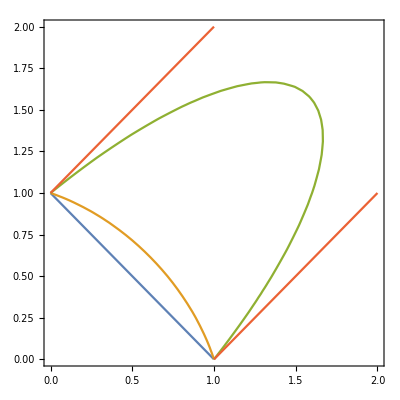

```mathematica
ContourPlot[{deltaqTargFunc[0]==0,deltaqTargFunc[1/3]==0,deltaqTargFunc[0.9]==0,deltaqTargFunc[1]==0},{kT,0,2},{lT,0,2}]
```

```mathematica
JacEta  Jacl Jack integral//.lsol[[1]]//.ksol[[1]]//FullSimplify
```

(4 kp^(-1-α) kT^(1-2 eps) lp^(1-α) lT^(1-2 eps) Sin[phi]^(-2 eps))/(√(-(-1+eta) eta) (lp^2+lT^2) (kT^2 lp^2+kp^2 lT^2-2 kp kT lp lT Cos[phi]))

```mathematica
integralfull =JacEta  Jacl Jack integral//.lsol[[1]]//.ksol[[1]]//.ReplEta//FullSimplify
```

(4^(1-eps) (-(-1+eta) eta)^(-1/2-eps) kp^(-1-α) kT^(1-2 eps) lp^(1-α) lT^(1-2 eps))/((lp^2+lT^2) (kT^2 lp^2+2 (-1+2 eta) kp kT lp lT+kp^2 lT^2))

```mathematica
etasol=eta//.Solve[(deltaqTarg//.ReplEta)==0,eta][[1]]
JacqT=1/D[(deltaqTarg//.ReplEta),eta]
```

(-1+kT^2+2 kT lT+lT^2)/(4 kT lT)

-1/(4 kT lT)

```mathematica
resnotheta=FullSimplify[integralfull JacqT//.{eta-> etasol},kT>0 && lT>0]
```

-(4^(1+eps) kp^(-1-α) kT lp^(1-α) lT (-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^(-1/2-eps))/((lp^2+lT^2) (lp (kp (-1+kT^2)+kT^2 lp)+kp (kp+lp) lT^2))

```mathematica
res=FullSimplify[integralfull JacqT//.{eta-> etasol},kT>0 && lT>0]HeavisideTheta[1+kT-lT,1-kT+lT,-1+kT+lT] .12
```

-(4^(1+eps) .12 kp^(-1-α) kT lp^(1-α) lT (-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^(-1/2-eps) HeavisideTheta[1+kT-lT,1-kT+lT,-1+kT+lT])/((lp^2+lT^2) (lp (kp (-1+kT^2)+kT^2 lp)+kp (kp+lp) lT^2))

```mathematica
ReplPerpSym={kT-> (κ+λ)/2,lT-> (κ-λ)/2};
```

```mathematica
respm=res//.ReplPerpSym//FullSimplify
```

-(4^(2+eps) .12 kp^(-1-α) lp^(1-α) (κ-λ) (κ+λ) (-(-1+κ^2) (-1+λ^2))^(-1/2-eps) HeavisideTheta[-1+κ,1-λ,1+λ])/((4 lp^2+(κ-λ)^2) (kp^2 (κ-λ)^2+lp^2 (κ+λ)^2+2 kp lp (-2+κ^2+λ^2)))

```mathematica
etasol//.{kT-> (κ+λ)/2,lT-> (κ-λ)/2}//FullSimplify
```

(-1+κ^2)/(κ^2-λ^2)

```mathematica
funclp=1/(1+lp)
funclpsol=Solve[x==funclp,lp][[1]]
funckp=1/(1+kp)
funckpsol=Solve[y==funckp,kp][[1]]
```

1/(1+lp)

{lp→(1-x)/x}

1/(1+kp)

{kp→(1-y)/y}

```mathematica
Jaclp=D[funclp,lp]//.funclpsol//FullSimplify
Jackp=D[funckp,kp]//.funckpsol//FullSimplify
```

-x^2

-y^2

```mathematica
restmp=Simplify[Jaclp Jackp respm//.funclpsol//.funckpsol,x>0&&y>0]
```

-(4^(2+eps) .12 (-1+1/x)^(1-α) x^2 (-1+1/y)^(-1-α) y^2 (κ-λ) (κ+λ) (-(-1+κ^2) (-1+λ^2))^(-1/2-eps) HeavisideTheta[-1+κ,1-λ,1+λ])/(((4 (-1+x)^2)/x^2+(κ-λ)^2) (((-1+y)^2 (κ-λ)^2)/y^2+((-1+x)^2 (κ+λ)^2)/x^2+(2 (-1+x) (-1+y) (-2+κ^2+λ^2))/(x y)))

```mathematica
ressub=restmp//.{κ-> 1/γ}//FullSimplify
```

-(4^(2+eps) .12 (-1+1/x)^(1-α) x^2 (-1+1/y)^(-1-α) y^2 (1/γ-λ) (1/γ+λ) (-(-1+1/γ^2) (-1+λ^2))^(-1/2-eps) HeavisideTheta[-1+1/γ,1-λ,1+λ])/(((4 (-1+x)^2)/x^2+(1/γ-λ)^2) (((-1+y)^2 (1/γ-λ)^2)/y^2+((-1+x)^2 (1/γ+λ)^2)/x^2+(2 (-1+x) (-1+y) (-2+1/γ^2+λ^2))/(x y)))

## Mappings

```mathematica
Get["HEP.m"]
```

HEP Package

by Sebastian Sapeta

```mathematica
fs={(x1+x2)/2,(x1-x2)/2};
vars={x1,x2}; (* new variables *)
```

```mathematica
JacobianMatrix[fs,vars]//MatrixForm
JacobianDeterminant[fs,vars]
```

(1/2 | 1/2
1/2 | -1/2)

-1/2

```mathematica
resnotheta
```

-(4^(1+eps) kp^(-1-α) kT lp^(1-α) lT (-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^(-1/2-eps))/((lp^2+lT^2) (lp (kp (-1+kT^2)+kT^2 lp)+kp (kp+lp) lT^2))

```mathematica
resnotheta//.eps-> -1/2-EPS
```

-(4^(1/2-EPS) kp^(-1-α) kT lp^(1-α) lT (-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^EPS)/((lp^2+lT^2) (lp (kp (-1+kT^2)+kT^2 lp)+kp (kp+lp) lT^2))

```mathematica
resnotheta//.{Plus[Rational[-1,2],Times[-1,eps]]-> EPS}
```

-(4^(1+eps) kp^(-1-α) kT lp^(1-α) lT (-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^EPS)/((lp^2+lT^2) (lp (kp (-1+kT^2)+kT^2 lp)+kp (kp+lp) lT^2))

### Step 1: transformation of transverse components

```mathematica
ReplTransInv={kT->(-1-yT+xT yT)/(2 (-1+xT)),lT->(-1+yT-xT yT)/(2 (-1+xT))};
ReplTrans=InvertReplacement[ReplTransInv,{xT,yT}]
JacTrans=JacobianDeterminant@@FuncFromReplRule[ReplTrans,ReplTransInv]
```

{xT→(-1+kT+lT)/(kT+lT),yT→kT-lT}

-1/(2 (-1+xT)^2)

```mathematica
ReplFreezeEps={eps-> -1/2-EPS};
```

```mathematica
integrandstep1=JacTrans resnotheta//.ReplFreezeEps//.ReplTransInv//FullSimplify
```

-(4^(1-EPS) kp^(-1-α) lp^(1-α) (-1+(-1+xT) yT) (1+(-1+xT) yT) (((-2+xT) xT (-1+yT^2))/(-1+xT)^2)^EPS)/((4 lp^2 (-1+xT)^2+(1+(-1+xT) yT)^2) ((kp+kp (-1+xT) yT)^2+lp^2 (1+yT-xT yT)^2+2 kp lp (-1+yT^2+(-2+xT) xT (-2+yT^2))))

```mathematica
(-1+yT^2)//.{yT-> (kp-lp)/(kp+lp)}//FullSimplify
```

-(4 kp lp)/(kp+lp)^2

```mathematica
integrandstep1=integrandstep1//.{Power[x_Integer+p_,i_.]/;x<0-> Power[-1,i] Power[-x-p,i]}
```

-(4^(1-EPS) kp^(-1-α) lp^(1-α) (-1+(-1+xT) yT) (1+(-1+xT) yT) (((-2+xT) xT (-1+yT^2))/(1-xT)^2)^EPS)/((4 lp^2 (1-xT)^2+(1+(-1+xT) yT)^2) ((kp+kp (-1+xT) yT)^2+lp^2 (1+yT-xT yT)^2+2 kp lp (-1+yT^2+(-2+xT) xT (-2+yT^2))))

#### Limits and divergences

We see that the points (1, 0), (0, 1) and (inf, inf) in (kT, lT) plane tranform to (1,0), (0,1) and (1,[-1:1]) in the (xT, yT) space

```mathematica
ReplTrans//.{kT-> 1, lT-> 0}
ReplTrans//.{kT-> 0, lT-> 1}
Limit[xT//.ReplTrans, kT-> Infinity]
```

{xT→0,yT→1}

{xT→0,yT→-1}

1

```mathematica
Solve[{kT==kp/(kp+lp),lT==lp/(kp+lp)}//.ReplTransInv,{xT, yT}]
```

{{xT→0,yT→(kp-lp)/(kp+lp)}}

### Step 2: split on manifold in yT space

```mathematica
ReplybarTu={ybarT->(yT-(kp-lp)/(kp+lp))/(1-(kp-lp)/(kp+lp))};
ReplybarTd={ybarT->(yT-(kp-lp)/(kp+lp))/(-1-(kp-lp)/(kp+lp))};
ReplybarTuInv=InvertReplacement[ReplybarTu,{yT}]
ReplybarTdInv=InvertReplacement[ReplybarTd,{yT}]
JacybarTu=-JacobianDeterminant@@FuncFromReplRule[ReplybarTu,ReplybarTuInv]
JacybarTd=JacobianDeterminant@@FuncFromReplRule[ReplybarTd,ReplybarTdInv]
```

{yT→(kp-lp+2 lp ybarT)/(kp+lp)}

{yT→(kp-lp-2 kp ybarT)/(kp+lp)}

-(2 lp)/(kp+lp)

-(2 kp)/(kp+lp)

```mathematica
integrandstep2u=JacybarTu integrandstep1//.ReplybarTuInv//FullSimplify//PowerExpand
integrandstep2d=JacybarTd integrandstep1//.ReplybarTdInv//FullSimplify;
```

(8 kp^(-1-α) lp^(2+EPS-α) (kp+lp)^(-1-2 EPS) (-2+xT)^EPS (-1+xT)^(-2 EPS) xT^EPS (-1+ybarT)^EPS (kp+lp ybarT)^EPS (kp (-2+xT)-lp xT+2 lp (-1+xT) ybarT) (kp xT+lp (2-xT+2 (-1+xT) ybarT)))/((kp^2 xT^2+2 kp lp xT (4-3 xT+2 (-1+xT) ybarT)+lp^2 (xT+2 ybarT-2 xT ybarT)^2) (8 kp lp^3 (-1+xT)^2+4 lp^4 (-1+xT)^2+kp^2 xT^2+2 kp lp xT (2-xT+2 (-1+xT) ybarT)+lp^2 (4 kp^2 (-1+xT)^2+(-2+xT+2 ybarT-2 xT ybarT)^2)))

```mathematica
integrandstep1//.ReplybarTdInv//.kp-> 0
```

(0^(-1+EPS-α) 4^(1-EPS) lp^(-1-α) (2-xT))/((4 lp^2 (1-xT)^2+(2-xT)^2) xT)

```mathematica
Series[integrandstep1//.ReplybarTdInv//PowerExpand,{kp,0,0}]
```

kp^(-1-α) ((kp (-1+ybarT))/lp)^EPS ((4 lp^(-1-α) (1-xT)^(-2 EPS) (2-xT) (-2+xT)^EPS xT^(-1+EPS))/(4 lp^2 (1-xT)^2+(2-xT)^2)+O[kp]^1)

### Step 3: split at yT=1/2

```mathematica
ReplyTu={yT-> 2(1-ybarT)};
ReplyTd={yT-> 2ybarT};
ReplyTuInv=InvertReplacement[ReplyTu,{ybarT}]
ReplyTdInv=InvertReplacement[ReplyTd,{ybarT}]
JacyTu=JacobianDeterminant@@FuncFromReplRule[ReplyTu,ReplyTuInv]
JacyTd=JacobianDeterminant@@FuncFromReplRule[ReplyTd,ReplyTdInv]
```

{ybarT→(2-yT)/2}

{ybarT→yT/2}

-1/2

1/2

```mathematica
integrandstep2u
```

(8 kp^(-1-α) lp^(2+EPS-α) (kp+lp)^(-1-2 EPS) (-2+xT)^EPS (-1+xT)^(-2 EPS) xT^EPS (-1+ybarT)^EPS (kp+lp ybarT)^EPS (kp (-2+xT)-lp xT+2 lp (-1+xT) ybarT) (kp xT+lp (2-xT+2 (-1+xT) ybarT)))/((kp^2 xT^2+2 kp lp xT (4-3 xT+2 (-1+xT) ybarT)+lp^2 (xT+2 ybarT-2 xT ybarT)^2) (8 kp lp^3 (-1+xT)^2+4 lp^4 (-1+xT)^2+kp^2 xT^2+2 kp lp xT (2-xT+2 (-1+xT) ybarT)+lp^2 (4 kp^2 (-1+xT)^2+(-2+xT+2 ybarT-2 xT ybarT)^2)))

```mathematica
integrandstep3u1=JacyTu integrandstep2u//.ReplyTuInv//.{xbarT-> xT}//FullSimplify;
integrandstep3u0=JacyTd integrandstep2u//.ReplyTdInv//.{xbarT-> xT}//FullSimplify;integrandstep3d=integrandstep2d//.{ybarT-> yT}//FullSimplify;
```

### Step 4: compressing limits of kp, lp

```mathematica
TransformLongitudinalComponents[integral_]:=Module[{Repl,ReplInv,Jacobian},
ReplInv={kp-> x/(1-x),lp-> y/(1-y)};
Repl=InvertReplacement[ReplInv,{x,y}];
Jacobian=JacobianDeterminant@@FuncFromReplRule[Repl,ReplInv];
Return[Jacobian integral//.ReplInv//FullSimplify];
]
```

```mathematica
Iu1=TransformLongitudinalComponents[integrandstep3u1];
Iu0=TransformLongitudinalComponents[integrandstep3u0];
Id=TransformLongitudinalComponents[integrandstep3d];
```

```mathematica
resnotheta
```

-(4^(1+eps) kp^(-1-α) kT lp^(1-α) lT (-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^(-1/2-eps))/((lp^2+lT^2) (lp (kp (-1+kT^2)+kT^2 lp)+kp (kp+lp) lT^2))

```mathematica
HeavisideTheta[lT+kT-1,1-(kT-lT),1-(lT-kT)](-(1-(kT-lT)^2) (1-(kT+lT)^2))^(-1/2-eps)//.{eps-> -0.1}//.{kT-> 99.63484326443466, lT-> 99.40661274338224}
```

0.0147959

```mathematica
HeavisideTheta[lT+kT-1,1-(kT-lT),1-(lT-kT)](-(1-(kT-lT)^2) (1-(kT+lT)^2))^(-1/2-eps)//.{eps-> -0.1}//.{kT-> 99.63484326443466, lT-> 99.40661274338224}
```

0.0147959

```mathematica
Plot3D[Im[HeavisideTheta[lT+kT-1,1-(kT-lT),1-(lT-kT)](-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^(-1/2-eps)]//.{eps-> -1},{kT,0,100},{lT,0,100}]
```

-Graphics3D-

## Prepare integrals for SecDec

```mathematica
PrepareForSecDec[integral_]:=Block[{int,ReplSamePowers1,int1,constfac,pows},
ReplSamePowers1={pow[i1_,j_] pow[i2_,j_]-> pow[i1 i2, j]};

int1=int1//.Power[expr__,Plus[n_.,i_. EPS]]->   Power[expr,n]pow[expr^i,EPS];
int1=int1//.pow[expr1__,EPS]pow[expr2__,EPS]-> pow[expr1 expr2, EPS];
int1=List@@integral;
int1=Replace[int1,Power[i_,j_.]-> pow[i,j],1];
int1=Times@@int1;
int1=int1//.ReplSamePowers1;
int1=int1/.{pow[i_,j_]:> pow[Together[i],j]};
int1=int1/.{pow[expr__,i_]:>  pow[Numerator[expr],i]pow[Denominator[expr],-i]};
int1=int1//.ReplSamePowers1;
int1=int1//.pow[-1+y_,i_] pow[-y_,j_]/;(i==-j)-> pow[1-y,i] pow[y,j];

(* put constant factors into const[] *)
constfac=int1/.pow[__]-> 1/.Power[p_,i_]-> const[p,i];
pows=Times@@Cases[int1,pow[__]];
int1=constfac pows;
int1=int1/.{pow[x_Integer,i_]-> const[x,i]};
Return[int1];
]
```

```mathematica
Id
```

(8 (x/(1-x))^-α (y/(1-y))^(1-α) ((x (-2+xT) xT (-1+y) (-1+yT) ((-1+x) y+x (-1+y) yT))/((-1+xT)^2 (x+y-2 x y)^2))^EPS ((xT y)/(1-y)+(x (-2+xT+2 yT-2 xT yT))/(-1+x)) (-((-2+xT) y)/(-1+y)+(x (xT+2 yT-2 xT yT))/(-1+x)))/((-1+x) (-1+y) (x+y-2 x y) ((xT^2 y^2)/(-1+y)^2+(2 x xT y (4-3 xT+2 (-1+xT) yT))/((-1+x) (-1+y))+(x^2 (xT+2 yT-2 xT yT)^2)/(-1+x)^2) ((((-2+xT)^2+(4 x^2 (-1+xT)^2)/(-1+x)^2) y^2)/(-1+y)^2+(8 x (-1+xT)^2 y^3)/((-1+x) (-1+y)^3)+(4 (-1+xT)^2 y^4)/(-1+y)^4+(2 x (-2+xT) y (-xT+2 (-1+xT) yT))/((-1+x) (-1+y))+(x^2 (xT+2 yT-2 xT yT)^2)/(-1+x)^2))

```mathematica
int1//.{x->0,y->0,xT-> 0,yT-> 0}
```

pow[0,-1] pow[0,1] pow[0,-1/2-eps] pow[0,1/2+eps] pow[0,1-α] pow[0,-α] pow[1,-1+α] pow[1,α]

```mathematica
IdToSecDec=PrepareForSecDec[Id]
```

pow[1-x,α] pow[x,-α] pow[1-y,-1+α] pow[y,1-α] pow[(-1+xT)^2 (-x-y+2 x y)^2,-EPS] pow[x (-2+xT) xT (-1+y) (-1+yT) (-y+x y-x yT+x y yT),EPS] pow[8 (-1+x)^3 (-1+y)^5 (x xT+2 y-2 x y-xT y+2 x yT-2 x xT yT-2 x y yT+2 x xT y yT) (-2 x+x xT+2 x y-xT y+2 x yT-2 x xT yT-2 x y yT+2 x xT y yT),1] pow[-(-1+x)^2 (-1+y)^2 (-x-y+2 x y) (x^2 xT^2+8 x xT y-8 x^2 xT y-6 x xT^2 y+4 x^2 xT^2 y-8 x xT y^2+8 x^2 xT y^2+xT^2 y^2+4 x xT^2 y^2-4 x^2 xT^2 y^2+4 x^2 xT yT-4 x^2 xT^2 yT-4 x xT y yT-4 x^2 xT y yT+4 x xT^2 y yT+4 x^2 xT^2 y yT+4 x xT y^2 yT-4 x xT^2 y^2 yT+4 x^2 yT^2-8 x^2 xT yT^2+4 x^2 xT^2 yT^2-8 x^2 y yT^2+16 x^2 xT y yT^2-8 x^2 xT^2 y yT^2+4 x^2 y^2 yT^2-8 x^2 xT y^2 yT^2+4 x^2 xT^2 y^2 yT^2) (x^2 xT^2+4 x xT y-4 x^2 xT y-2 x xT^2 y-2 x^2 xT^2 y+4 y^2-8 x y^2+8 x^2 y^2-4 xT y^2-4 x xT y^2+xT^2 y^2+4 x xT^2 y^2+5 x^2 xT^2 y^2-8 y^3+24 x y^3-24 x^2 y^3+8 xT y^3-20 x xT y^3+28 x^2 xT y^3-2 xT^2 y^3+6 x xT^2 y^3-16 x^2 xT^2 y^3+8 y^4-24 x y^4+20 x^2 y^4-12 xT y^4+36 x xT y^4-32 x^2 xT y^4+5 xT^2 y^4-16 x xT^2 y^4+16 x^2 xT^2 y^4+4 x^2 xT yT-4 x^2 xT^2 yT+8 x y yT-8 x^2 y yT-12 x xT y yT-4 x^2 xT y yT+4 x xT^2 y yT+12 x^2 xT^2 y yT-24 x y^2 yT+24 x^2 y^2 yT+36 x xT y^2 yT-12 x^2 xT y^2 yT-12 x xT^2 y^2 yT-12 x^2 xT^2 y^2 yT+24 x y^3 yT-24 x^2 y^3 yT-36 x xT y^3 yT+20 x^2 xT y^3 yT+12 x xT^2 y^3 yT+4 x^2 xT^2 y^3 yT-8 x y^4 yT+8 x^2 y^4 yT+12 x xT y^4 yT-8 x^2 xT y^4 yT-4 x xT^2 y^4 yT+4 x^2 yT^2-8 x^2 xT yT^2+4 x^2 xT^2 yT^2-16 x^2 y yT^2+32 x^2 xT y yT^2-16 x^2 xT^2 y yT^2+24 x^2 y^2 yT^2-48 x^2 xT y^2 yT^2+24 x^2 xT^2 y^2 yT^2-16 x^2 y^3 yT^2+32 x^2 xT y^3 yT^2-16 x^2 xT^2 y^3 yT^2+4 x^2 y^4 yT^2-8 x^2 xT y^4 yT^2+4 x^2 xT^2 y^4 yT^2),-1]

```mathematica
IdToSecDec//.{x->0, y-> 0,xT-> 0, yT-> 0}
```

pow[0,-1] pow[0,1] pow[0,-EPS] pow[0,EPS] pow[0,1-α] pow[0,-α] pow[1,-1+α] pow[1,α]

```mathematica
tmp=(Id/IdToSecDec)/.{pow[i_,j_]|const[i_,j_]:>  Power[i,j]}//PowerExpand//FullSimplify;
tmp/.Power[p_,2 eps] Power[ q_,-2 eps]-> Power[p /q, 2 eps]//FullSimplify
```

(-1)^(1+2 eps)

```mathematica
Iu1
```

-((4^(1-EPS) (x/(1-x))^(-1-α) (-2+xT)^EPS (-1+xT)^(-2 EPS) xT^EPS (y/(1-y))^(2+EPS-α) ((x+y-2 x y)/((-1+x) (-1+y)))^(-1-2 EPS) ((x (2+y (-4+yT))-y (-2+yT))/((-1+x) (-1+y)))^EPS (-yT)^EPS (((-2+xT) (x+y-2 x y))/(-1+x)+(-1+xT) y yT) ((x xT)/(1-x)+(y (xT+yT-xT yT))/(1-y)))/((-1+x)^2 (-1+y) (((x+y-2 x y)^2 (xT^2+(4 (-1+xT)^2 y^2)/(-1+y)^2))/(-1+x)^2-(2 (-1+xT) xT y (-y+x (-1+2 y)) yT)/(-1+x)+(-1+xT)^2 y^2 yT^2) ((x^2 xT^2)/(-1+x)^2-(2 x xT y (-2+xT+(-1+xT) yT))/((-1+x) (-1+y))+(y^2 (-2+xT+yT-xT yT)^2)/(-1+y)^2)))

```mathematica
Iu1//.Power[expr__,Plus[n_.,i_. EPS]]->   Power[expr,n]pow[expr^i,EPS]
```

-((4 (x/(1-x))^(-1-α) (y/(1-y))^(2-α) (((-2+xT) (x+y-2 x y))/(-1+x)+(-1+xT) y yT) ((x xT)/(1-x)+(y (xT+yT-xT yT))/(1-y)) pow[1/4,EPS] pow[-2+xT,EPS] pow[1/(-1+xT)^2,EPS] pow[xT,EPS] pow[y/(1-y),EPS] pow[((-1+x)^2 (-1+y)^2)/(x+y-2 x y)^2,EPS] pow[(x (2+y (-4+yT))-y (-2+yT))/((-1+x) (-1+y)),EPS] pow[-yT,EPS])/((-1+x) (x+y-2 x y) (((x+y-2 x y)^2 (xT^2+(4 (-1+xT)^2 y^2)/(-1+y)^2))/(-1+x)^2-(2 (-1+xT) xT y (-y+x (-1+2 y)) yT)/(-1+x)+(-1+xT)^2 y^2 yT^2) ((x^2 xT^2)/(-1+x)^2-(2 x xT y (-2+xT+(-1+xT) yT))/((-1+x) (-1+y))+(y^2 (-2+xT+yT-xT yT)^2)/(-1+y)^2)))

```mathematica
PrepareForSecDec[integral_]:=Block[{int,ReplSamePowers1,int1,constfac,pows},
ReplSamePowers1={pow[i1_,j_] pow[i2_,j_]-> pow[i1 i2, j]};

int1=integral//.Power[expr__,Plus[n_.,i_. EPS]]->   Power[expr,n]pow[expr^i,EPS];
int1=int1//.pow[expr1__,EPS]pow[expr2__,EPS]-> pow[expr1 expr2, EPS];
int1=int1/.pow-> Power;
int1=List@@int1;
int1=Replace[int1,Power[i_,j_.]-> pow[i,j],1];
int1=Times@@int1;
int1=int1//.ReplSamePowers1;
int1=int1/.{pow[i_,j_]:> pow[Together[i],j]};
int1=int1/.{pow[expr__,i_]:>  pow[Numerator[expr],i]pow[Denominator[expr],-i]};
int1=int1//.ReplSamePowers1;
int1=int1//.pow[-1+y_,i_] pow[-y_,j_]/;(i==-j)-> pow[1-y,i] pow[y,j];

(* put constant factors into const[] *)
constfac=int1/.pow[__]-> 1/.Power[p_,i_]-> const[p,i];
(*constfac=constfac /. const[p_,i_]const[q_,j_]-> p^i q^j/.Power[p_,i_]-> const[p,i];*)
pows=Times@@Cases[int1,pow[__]];
int1=constfac pows;
int1=int1/.{pow[x_Integer,i_]-> const[x,i]};
constfac=Times@@Cases[int1,const[__]];
int1=int1 /. const[p_,i_]const[q_,j_]->const[ p^i q^j]/.const[Power[p_,i_]]-> const[p,i];
Return[int1];
]
```

```mathematica
Iu1ToSecDec=PrepareForSecDec[Iu1]
```

const[4,1-EPS] pow[1-x,1+α] pow[x,-1-α] pow[1-y,-2+α] pow[y,2-α] pow[(-1+xT)^2 (-x-y+2 x y)^2,-EPS] pow[(-1+x) (-2+xT) xT y yT (2 x+2 y-4 x y-y yT+x y yT),EPS] pow[-(-1+x)^3 (-1+y)^4 (x xT+xT y-2 x xT y+y yT-x y yT-xT y yT+x xT y yT) (-2 x+x xT-2 y+4 x y+xT y-2 x xT y+y yT-x y yT-xT y yT+x xT y yT),1] pow[-(-1+x)^2 (-1+y) (-x-y+2 x y) (x^2 xT^2+4 x xT y-4 x^2 xT y-2 x xT^2 y+4 y^2-8 x y^2+4 x^2 y^2-4 xT y^2+4 x xT y^2+xT^2 y^2+2 x xT y yT-2 x^2 xT y yT-2 x xT^2 y yT+2 x^2 xT^2 y yT-4 y^2 yT+8 x y^2 yT-4 x^2 y^2 yT+6 xT y^2 yT-14 x xT y^2 yT+8 x^2 xT y^2 yT-2 xT^2 y^2 yT+6 x xT^2 y^2 yT-4 x^2 xT^2 y^2 yT+y^2 yT^2-2 x y^2 yT^2+x^2 y^2 yT^2-2 xT y^2 yT^2+4 x xT y^2 yT^2-2 x^2 xT y^2 yT^2+xT^2 y^2 yT^2-2 x xT^2 y^2 yT^2+x^2 xT^2 y^2 yT^2) (x^2 xT^2+2 x xT^2 y-6 x^2 xT^2 y+4 x^2 y^2-8 x^2 xT y^2+xT^2 y^2-8 x xT^2 y^2+17 x^2 xT^2 y^2+8 x y^3-16 x^2 y^3-16 x xT y^3+32 x^2 xT y^3-2 xT^2 y^3+18 x xT^2 y^3-28 x^2 xT^2 y^3+4 y^4-16 x y^4+16 x^2 y^4-8 xT y^4+32 x xT y^4-32 x^2 xT y^4+5 xT^2 y^4-20 x xT^2 y^4+20 x^2 xT^2 y^4+2 x xT y yT-2 x^2 xT y yT-2 x xT^2 y yT+2 x^2 xT^2 y yT+2 xT y^2 yT-10 x xT y^2 yT+8 x^2 xT y^2 yT-2 xT^2 y^2 yT+10 x xT^2 y^2 yT-8 x^2 xT^2 y^2 yT-4 xT y^3 yT+14 x xT y^3 yT-10 x^2 xT y^3 yT+4 xT^2 y^3 yT-14 x xT^2 y^3 yT+10 x^2 xT^2 y^3 yT+2 xT y^4 yT-6 x xT y^4 yT+4 x^2 xT y^4 yT-2 xT^2 y^4 yT+6 x xT^2 y^4 yT-4 x^2 xT^2 y^4 yT+y^2 yT^2-2 x y^2 yT^2+x^2 y^2 yT^2-2 xT y^2 yT^2+4 x xT y^2 yT^2-2 x^2 xT y^2 yT^2+xT^2 y^2 yT^2-2 x xT^2 y^2 yT^2+x^2 xT^2 y^2 yT^2-2 y^3 yT^2+4 x y^3 yT^2-2 x^2 y^3 yT^2+4 xT y^3 yT^2-8 x xT y^3 yT^2+4 x^2 xT y^3 yT^2-2 xT^2 y^3 yT^2+4 x xT^2 y^3 yT^2-2 x^2 xT^2 y^3 yT^2+y^4 yT^2-2 x y^4 yT^2+x^2 y^4 yT^2-2 xT y^4 yT^2+4 x xT y^4 yT^2-2 x^2 xT y^4 yT^2+xT^2 y^4 yT^2-2 x xT^2 y^4 yT^2+x^2 xT^2 y^4 yT^2),-1]

```mathematica
Iu1ToSecDec//.{x->0, y-> 0,xT-> 0, yT-> 0}
```

const[1,-1+EPS] const[4,1-EPS] pow[0,-1] pow[0,1] pow[0,-EPS] pow[0,EPS] pow[0,-1-α] pow[0,2-α] pow[1,-2+α] pow[1,1+α]

```mathematica
(Iu1/Iu1ToSecDec)/.pow[i_,j_]|const[i_,j_]-> Power[i,j]//PowerExpand//FullSimplify
```

(-1)^EPS (1-y)^-EPS (-1+y)^EPS (x+y-2 x y)^(-2 EPS) (-y+x (-1+2 y))^(2 EPS)

```mathematica
Iu0
```

(2^(3+2 eps) (x/(1-x))^(-1-α) (-2+xT)^(-1/2-eps) (-1+xT)^(1+2 eps) xT^(-1/2-eps) (y/(1-y))^(3/2-eps-α) ((x+y-2 x y)/((-1+x) (-1+y)))^(2 eps) (-2+yT)^(-1/2-eps) (-(2 x)/(-1+x)+(y yT)/(1-y))^(-1/2-eps) ((x xT)/(1-x)+(y (-2+xT+yT-xT yT))/(-1+y)) (-(x (-2+xT))/(-1+x)+(y (xT+yT-xT yT))/(-1+y)))/((-1+x)^2 (-1+y)^2 ((x^2 xT^2)/(-1+x)^2+(2 x xT y (4+xT (-3+yT)-yT))/((-1+x) (-1+y))+(y^2 (xT+yT-xT yT)^2)/(-1+y)^2) ((x^2 xT^2)/(-1+x)^2+(8 x (-1+xT)^2 y^3)/((-1+x) (-1+y)^3)+(4 (-1+xT)^2 y^4)/(-1+y)^4+(2 x xT y (2+xT (-1+yT)-yT))/((-1+x) (-1+y))+(y^2 ((4 x^2 (-1+xT)^2)/(-1+x)^2+(-2+xT+yT-xT yT)^2))/(-1+y)^2))

```mathematica
Iu0ToSecDec=PrepareForSecDec[Iu0](*/.pow[p__,-2 EPS]-> pow[p^2,EPS]*)(*/.{Power[x_Integer+p_,i_.]/;x<0:>  Power[-1,i] Power[-x-p,i]}*)
```

const[2,2-EPS] pow[1-x,1+α] pow[x,-1-α] pow[1-y,-2+α] pow[y,2-α] pow[2 (-1+xT)^2 (-x-y+2 x y)^2,-EPS] pow[(-1+x) (-2+xT) xT y (-2+yT) (-2 x+2 x y-y yT+x y yT),EPS] pow[(-1+x)^3 (-1+y)^5 (2 x-x xT-2 x y+xT y+y yT-x y yT-xT y yT+x xT y yT) (-x xT-2 y+2 x y+xT y+y yT-x y yT-xT y yT+x xT y yT),1] pow[-(-1+x)^2 (-1+y)^2 (-x-y+2 x y) (x^2 xT^2+8 x xT y-8 x^2 xT y-6 x xT^2 y+4 x^2 xT^2 y-8 x xT y^2+8 x^2 xT y^2+xT^2 y^2+4 x xT^2 y^2-4 x^2 xT^2 y^2-2 x xT y yT+2 x^2 xT y yT+2 x xT^2 y yT-2 x^2 xT^2 y yT+2 xT y^2 yT-2 x xT y^2 yT-2 xT^2 y^2 yT+2 x xT^2 y^2 yT+y^2 yT^2-2 x y^2 yT^2+x^2 y^2 yT^2-2 xT y^2 yT^2+4 x xT y^2 yT^2-2 x^2 xT y^2 yT^2+xT^2 y^2 yT^2-2 x xT^2 y^2 yT^2+x^2 xT^2 y^2 yT^2) (x^2 xT^2+4 x xT y-4 x^2 xT y-2 x xT^2 y-2 x^2 xT^2 y+4 y^2-8 x y^2+8 x^2 y^2-4 xT y^2-4 x xT y^2+xT^2 y^2+4 x xT^2 y^2+5 x^2 xT^2 y^2-8 y^3+24 x y^3-24 x^2 y^3+8 xT y^3-20 x xT y^3+28 x^2 xT y^3-2 xT^2 y^3+6 x xT^2 y^3-16 x^2 xT^2 y^3+8 y^4-24 x y^4+20 x^2 y^4-12 xT y^4+36 x xT y^4-32 x^2 xT y^4+5 xT^2 y^4-16 x xT^2 y^4+16 x^2 xT^2 y^4-2 x xT y yT+2 x^2 xT y yT+2 x xT^2 y yT-2 x^2 xT^2 y yT-4 y^2 yT+8 x y^2 yT-4 x^2 y^2 yT+6 xT y^2 yT-6 x xT y^2 yT-2 xT^2 y^2 yT-2 x xT^2 y^2 yT+4 x^2 xT^2 y^2 yT+8 y^3 yT-16 x y^3 yT+8 x^2 y^3 yT-12 xT y^3 yT+18 x xT y^3 yT-6 x^2 xT y^3 yT+4 xT^2 y^3 yT-2 x xT^2 y^3 yT-2 x^2 xT^2 y^3 yT-4 y^4 yT+8 x y^4 yT-4 x^2 y^4 yT+6 xT y^4 yT-10 x xT y^4 yT+4 x^2 xT y^4 yT-2 xT^2 y^4 yT+2 x xT^2 y^4 yT+y^2 yT^2-2 x y^2 yT^2+x^2 y^2 yT^2-2 xT y^2 yT^2+4 x xT y^2 yT^2-2 x^2 xT y^2 yT^2+xT^2 y^2 yT^2-2 x xT^2 y^2 yT^2+x^2 xT^2 y^2 yT^2-2 y^3 yT^2+4 x y^3 yT^2-2 x^2 y^3 yT^2+4 xT y^3 yT^2-8 x xT y^3 yT^2+4 x^2 xT y^3 yT^2-2 xT^2 y^3 yT^2+4 x xT^2 y^3 yT^2-2 x^2 xT^2 y^3 yT^2+y^4 yT^2-2 x y^4 yT^2+x^2 y^4 yT^2-2 xT y^4 yT^2+4 x xT y^4 yT^2-2 x^2 xT y^4 yT^2+xT^2 y^4 yT^2-2 x xT^2 y^4 yT^2+x^2 xT^2 y^4 yT^2),-1]

Write the integrals into a file:

```mathematica
Replxi={x-> x[1],y-> x[2], xT-> x[3], yT-> x[4]};
Replepap={EPS-> -1/2-ep, α-> ap};
(*Replepap={eps-> ep, α-> ap};*)
```

```mathematica
Write["PR53boundary.dat",{IdToSecDec,Iu0ToSecDec,Iu1ToSecDec}/.Replxi/.Replepap]
Close["PR53boundary.dat"];
```

## Numerical tests

```mathematica
ResetCuba[];
ReplEpsAlpha={eps->-1/3,α->-1/2};
IntOptions=Sequence[Verbose-> 0,MaxPoints-> 10000000,PrecisionGoal-> 2];
```

Suave::shdw: Symbol "Suave" appears in multiple contexts {"Cuba`", "Global`"}; definitions in context "Cuba`" may shadow or be shadowed by other definitions.

Original integral:

```mathematica
Vegas[Re[HeavisideTheta[lT+kT-1]resnotheta//.ReplEpsAlpha],{lp,0,1},{kp,0,1},{lT,0.001,100000},{kT,lT-1,lT+1},IntOptions]
```

Vegas::accuracy: Desired accuracy was not reached within 10049500 function evaluations.

{{-0.0276739,0.00189398,1.}}

```mathematica
Suave[Re[HeavisideTheta[lT+kT-1]resnotheta//.ReplEpsAlpha],{lp,0,1},{kp,0,1},{lT,0,100000},{kT,lT-1,lT+1},IntOptions]
```

Suave::accuracy: Desired accuracy was not reached within 10000000 function evaluations on 10000 subregions.

{{-16.8726,0.0229688,1.}}

After step 1:

```mathematica
Suave[Re[integrandstep1//.ReplEpsAlpha],{lp,0,1},{kp,0,1},{xT,0,1},{yT,-1,1},IntOptions]
```

Suave::success: Needed 69000 function evaluations on 69 subregions.

{{18.4446,0.183071,1.}}

Afterp step 2:

```mathematica
Suave[Re[integrandstep2u//.ReplEpsAlpha],{lp,0,1},{kp,0,1},{xT,0,1},{ybarT,0,1},IntOptions]
Suave[Re[integrandstep2d//.ReplEpsAlpha],{lp,0,1},{kp,0,1},{xT,0,1},{ybarT,0,1},IntOptions]
```

Suave::success: Needed 31000 function evaluations on 31 subregions.

{{-14.452,0.144494,1.}}

Suave::success: Needed 43000 function evaluations on 43 subregions.

{{-4.29767,0.0429437,1.}}

After step 3:

```mathematica
integrandstep3u1/.ReplEpsAlpha
```

(4 2^(2/3) lp^(7/3) (-1+xT)^(1/3) yT (kp+lp-(lp yT)/2)^(1/3) (-(kp+lp) (-2+xT)+lp (-1+xT) yT) (-(kp+lp) xT+lp (-1+xT) yT))/(√kp (kp+lp)^(2/3) (-2+xT)^(1/6) xT^(1/6) (-yT)^(7/6) √(2 (kp+lp)-lp yT) ((kp+lp)^2 (4 lp^2 (-1+xT)^2+xT^2)-2 lp (kp+lp) (-1+xT) xT yT+lp^2 (-1+xT)^2 yT^2) (kp^2 xT^2-2 kp lp xT (-2+xT+(-1+xT) yT)+lp^2 (-2+xT+yT-xT yT)^2))

```mathematica
numint3={Suave[Im[integrandstep3u0//.ReplEpsAlpha],{lp,0,1},{kp,0,1},{xT,0,1},{yT,0,1},IntOptions],
-Suave[Im[integrandstep3u1//.ReplEpsAlpha],{lp,0,1},{kp,0,1},{xT,0,1},{yT,0,1},IntOptions],
Suave[Im[integrandstep3d//.ReplEpsAlpha],{lp,0,1},{kp,0,1},{xT,0,1},{yT,0,1},IntOptions]}
```

Suave::success: Needed 1000 function evaluations on 1 subregions.

General::stop: Further output of Suave :: success will be suppressed during this calculation.

{{{-1.38713×10^-16,5.30856×10^-17,-999.}},{{7.06846×10^-16,-6.49277×10^-17,999.}},{{0.,7.02518×10^-18,-999.}}}

```mathematica
numint3={Suave[Re[integrandstep3u0//.ReplEpsAlpha],{lp,0,1},{kp,0,1},{xT,0,1},{yT,0,1},IntOptions],
-Suave[Re[integrandstep3u1//.ReplEpsAlpha],{lp,0,1},{kp,0,1},{xT,0,1},{yT,0,1},IntOptions],
Suave[Re[integrandstep3d//.ReplEpsAlpha],{lp,0,1},{kp,0,1},{xT,0,1},{yT,0,1},IntOptions]}
```

Suave::success: Needed 25000 function evaluations on 25 subregions.

Suave::success: Needed 13000 function evaluations on 13 subregions.

Suave::success: Needed 43000 function evaluations on 43 subregions.

General::stop: Further output of Suave :: success will be suppressed during this calculation.

{{{-8.52917,0.0839665,1.}},{{-5.90172,-0.0547093,-0.986088}},{{-4.29767,0.0429437,1.}}}

```mathematica
numint3[[All,1,1]]//Total
```

-18.7286

```mathematica
Suave[Re[integrandstep3d//.ReplEpsAlpha],{lp,0,10^5},{kp,0,10^5},{xT,0,1},{yT,0,1},IntOptions]
```

Suave::success: Needed 216000 function evaluations on 216 subregions.

{{-15.1786,0.151197,1.}}

```mathematica
Suave[Im[integrandstep3d//.ReplEpsAlpha],{lp,0,10^5},{kp,0,10^5},{xT,0,1},{yT,0,1},IntOptions]
```

Suave::success: Needed 1000 function evaluations on 1 subregions.

{{0.,7.02518×10^-18,-999.}}

```mathematica
Suave[Re[Id//.ReplEpsAlpha],{x,0,1},{y,0,1},{xT,0,1},{yT,0,1},IntOptions]
```

Suave::success: Needed 97000 function evaluations on 97 subregions.

{{-15.4847,0.151475,1.}}

```mathematica
Suave[Im[Id//.ReplEpsAlpha],{x,0,1},{y,0,1},{xT,0,1},{yT,0,1},IntOptions]
```

Suave::success: Needed 1000 function evaluations on 1 subregions.

{{0.,7.02518×10^-18,-999.}}

## Secdec more complex

### Form 1: original integral

```mathematica
(*NIntegrate[HeavisideTheta[1+kT-lT,1-kT+lT,-1+kT+lT]resnotheta//.ReplEpsAlpha,{lp,0,100000},{kp,0,100000},{lT,0,100000},{kT,0,100000}]*)
```

```mathematica
resnotheta
boundaries={1+(kT-lT)>=0,1-(kT-lT)>=0,1-(lT+kT)<=0, kp≥0, lp≥0}
singularities={{lp==0,lT==0},{kp==0},{kp==0,lp==0},{kT==kp/(kp+lp),lT==lp/(kp+lp)}}
```

-(4^(1+eps) kp^(-1-α) kT lp^(1-α) lT (-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^(-1/2-eps))/((lp^2+lT^2) (lp (kp (-1+kT^2)+kT^2 lp)+kp (kp+lp) lT^2))

{1+kT-lT≥0,1-kT+lT≥0,1-kT-lT≤0,kp≥0,lp≥0}

{{lp==0,lT==0},{kp==0},{kp==0,lp==0},{kT==kp/(kp+lp),lT==lp/(kp+lp)}}

```mathematica
resnotheta//.{lT-> 0, lp-> 0}
Series[resnotheta,{lT,0,1}]
```

Indeterminate

-(4^(1+eps) kp^(-1-α) kT (-1+2 kT^2-kT^4)^(-1/2-eps) lp^(-1-α) lT)/(-kp lp+kp kT^2 lp+kT^2 lp^2)+O[lT]^2

### Form 2: rotation in (xT, yT) space

```mathematica
ReplxTyT={xT->   kT+lT,yT-> kT-lT};
ReplxTyTInv=InvertReplacement[ReplxTyT,{kT,lT}]
FuncFromReplRule[ReplxTyT,ReplxTyTInv]
JacxTyT=-JacobianDeterminant@@FuncFromReplRule[ReplxTyT,ReplxTyTInv]
```

{kT→(xT+yT)/2,lT→(xT-yT)/2}

{{(xT+yT)/2,(xT-yT)/2},{xT,yT}}

1/2

```mathematica
integrand2=JacxTyT resnotheta//.ReplxTyTInv//FullSimplify
boundaries2=boundaries//.ReplxTyTInv//FullSimplify
singularities2=singularities//.ReplxTyTInv//FullSimplify
Solve[singularities2[[4]],{xT,yT}]
```

(2^(3+2 eps) kp^(-1-α) lp^(1-α) (-(-1+xT^2) (-1+yT^2))^(-1/2-eps) (-xT^2+yT^2))/((4 lp^2+(xT-yT)^2) (kp^2 (xT-yT)^2+lp^2 (xT+yT)^2+2 kp lp (-2+xT^2+yT^2)))

{1+yT≥0,yT≤1,xT≥1,kp≥0,lp≥0}

{{lp==0,xT==yT},{kp==0},{kp==0,lp==0},{xT+yT==(2 kp)/(kp+lp),xT==(2 lp)/(kp+lp)+yT}}

{{xT→1,yT→-1+(2 kp)/(kp+lp)}}

```mathematica
res=Join[boundaries2,#]&/@ singularities2
```

{{1+yT≥0,yT≤1,xT≥1,kp≥0,lp≥0,lp==0,xT==yT},{1+yT≥0,yT≤1,xT≥1,kp≥0,lp≥0,kp==0},{1+yT≥0,yT≤1,xT≥1,kp≥0,lp≥0,kp==0,lp==0},{1+yT≥0,yT≤1,xT≥1,kp≥0,lp≥0,xT+yT==(2 kp)/(kp+lp),xT==(2 lp)/(kp+lp)+yT}}

```mathematica
Reduce[#,{xT,yT}]&/@res
```

{kp≥0&&lp==0&&xT==1&&yT==1,kp==0&&lp≥0&&xT≥1&&-1≤yT≤1,kp==0&&lp==0&&xT≥1&&-1≤yT≤1,((lp==0&&kp>0&&xT==1)||(lp>0&&kp≥0&&xT==1))&&yT==(2 kp-kp xT-lp xT)/(kp+lp)}

### Form 3: xT ->1- 1/xT

```mathematica
ReplxbarT={xbarT->1-1/xT};
ReplxbarTInv=InvertReplacement[ReplxbarT,{xT}]
JacxbarT=JacobianDeterminant@@FuncFromReplRule[ReplxbarT,ReplxbarTInv]
```

{xT→1/(1-xbarT)}

1/(1-xbarT)^2

```mathematica
integrand3=JacxbarT integrand2//.ReplxbarTInv//FullSimplify
boundaries3=boundaries2//.ReplxbarTInv//FullSimplify
singularities3=singularities2//.ReplxbarTInv//FullSimplify
Solve[singularities3[[4]],{xbarT,yT}]
```

(2^(3+2 eps) kp^(-1-α) lp^(1-α) (((-2+xbarT) xbarT (-1+yT^2))/(-1+xbarT)^2)^(-1/2-eps) (-1+(-1+xbarT)^2 yT^2))/((4 lp^2 (-1+xbarT)^2+(1+(-1+xbarT) yT)^2) ((kp+kp (-1+xbarT) yT)^2+lp^2 (1+yT-xbarT yT)^2+2 kp lp (-1+yT^2+(-2+xbarT) xbarT (-2+yT^2))))

{1+yT≥0,yT≤1,xbarT/(-1+xbarT)≤0,kp≥0,lp≥0}

{{lp==0,1/(-1+xbarT)+yT==0},{kp==0},{kp==0,lp==0},{1/(1-xbarT)+yT==(2 kp)/(kp+lp),(2 lp)/(kp+lp)+1/(-1+xbarT)+yT==0}}

{{xbarT→0,yT→(kp-lp)/(kp+lp)}}

```mathematica
res=1/Cases[integrand3, x__^-1]
```

{4 lp^2 (-1+xbarT)^2+(1+(-1+xbarT) yT)^2,(kp+kp (-1+xbarT) yT)^2+lp^2 (1+yT-xbarT yT)^2+2 kp lp (-1+yT^2+(-2+xbarT) xbarT (-2+yT^2))}

```mathematica
res//.{lp-> 0, yT-> 1,xbarT-> 0}
```

{0,0}

```mathematica
res//.{xbarT->0,yT->(kp-lp)/(kp+lp)}//FullSimplify
```

{(4 lp^2 (1+(kp+lp)^2))/(kp+lp)^2,0}

### Form 4: split on manifold in yT space

```mathematica
ReplybarTu={ybarT->(yT-(kp-lp)/(kp+lp))/(1-(kp-lp)/(kp+lp))};
ReplybarTd={ybarT->(yT-(kp-lp)/(kp+lp))/(-1-(kp-lp)/(kp+lp))};
ReplybarTuInv=InvertReplacement[ReplybarTu,{yT}]
ReplybarTdInv=InvertReplacement[ReplybarTd,{yT}]
JacybarTu=JacobianDeterminant@@FuncFromReplRule[ReplybarTu,ReplybarTuInv]
JacybarTd=-JacobianDeterminant@@FuncFromReplRule[ReplybarTd,ReplybarTdInv]
```

{yT→(kp-lp+2 lp ybarT)/(kp+lp)}

{yT→(kp-lp-2 kp ybarT)/(kp+lp)}

(2 lp)/(kp+lp)

(2 kp)/(kp+lp)

```mathematica
integrand4u=JacybarTu integrand3//.ReplybarTuInv//FullSimplify;
integrand4d=JacybarTd integrand3//.ReplybarTdInv//FullSimplify;
```

```mathematica
integrand4u//Together
```

(8 kp^(-1-α) lp^(2-α) ((lp (-2+xbarT) xbarT (-1+ybarT) (kp+lp ybarT))/((kp+lp)^2 (-1+xbarT)^2))^(-1/2-eps) (-2 kp+kp xbarT-lp xbarT-2 lp ybarT+2 lp xbarT ybarT) (2 lp+kp xbarT-lp xbarT-2 lp ybarT+2 lp xbarT ybarT))/((kp+lp) (8 kp lp xbarT+kp^2 xbarT^2-6 kp lp xbarT^2+lp^2 xbarT^2-4 kp lp xbarT ybarT+4 lp^2 xbarT ybarT+4 kp lp xbarT^2 ybarT-4 lp^2 xbarT^2 ybarT+4 lp^2 ybarT^2-8 lp^2 xbarT ybarT^2+4 lp^2 xbarT^2 ybarT^2) (4 lp^2+4 kp^2 lp^2+8 kp lp^3+4 lp^4+4 kp lp xbarT-4 lp^2 xbarT-8 kp^2 lp^2 xbarT-16 kp lp^3 xbarT-8 lp^4 xbarT+kp^2 xbarT^2-2 kp lp xbarT^2+lp^2 xbarT^2+4 kp^2 lp^2 xbarT^2+8 kp lp^3 xbarT^2+4 lp^4 xbarT^2-8 lp^2 ybarT-4 kp lp xbarT ybarT+12 lp^2 xbarT ybarT+4 kp lp xbarT^2 ybarT-4 lp^2 xbarT^2 ybarT+4 lp^2 ybarT^2-8 lp^2 xbarT ybarT^2+4 lp^2 xbarT^2 ybarT^2))

```mathematica
den=1/Times@@Cases[Together[integrand4u],x__^-1]
den//.{xbarT-> 1,ybarT-> 0}//FullSimplify
den//.{xbarT-> 1,ybarT-> 1}//FullSimplify
den//.{xbarT-> 0,ybarT-> 0}//FullSimplify
den//.{xbarT-> 0,ybarT-> 1}//FullSimplify
```

(kp+lp) (8 kp lp xbarT+kp^2 xbarT^2-6 kp lp xbarT^2+lp^2 xbarT^2-4 kp lp xbarT ybarT+4 lp^2 xbarT ybarT+4 kp lp xbarT^2 ybarT-4 lp^2 xbarT^2 ybarT+4 lp^2 ybarT^2-8 lp^2 xbarT ybarT^2+4 lp^2 xbarT^2 ybarT^2) (4 lp^2+4 kp^2 lp^2+8 kp lp^3+4 lp^4+4 kp lp xbarT-4 lp^2 xbarT-8 kp^2 lp^2 xbarT-16 kp lp^3 xbarT-8 lp^4 xbarT+kp^2 xbarT^2-2 kp lp xbarT^2+lp^2 xbarT^2+4 kp^2 lp^2 xbarT^2+8 kp lp^3 xbarT^2+4 lp^4 xbarT^2-8 lp^2 ybarT-4 kp lp xbarT ybarT+12 lp^2 xbarT ybarT+4 kp lp xbarT^2 ybarT-4 lp^2 xbarT^2 ybarT+4 lp^2 ybarT^2-8 lp^2 xbarT ybarT^2+4 lp^2 xbarT^2 ybarT^2)

(kp+lp)^5

(kp+lp)^5

0

16 lp^4 (kp+lp)^3

```mathematica
den=1/Times@@Cases[integrand4d//.{xbarT-> xT, ybarT-> yT},x__^-1]
den//.{xT-> 1,yT-> 0}//FullSimplify
den//.{xT-> 1,yT-> 1}//FullSimplify
den//.{xT-> 0,yT-> 0}//FullSimplify
den//.{xT-> 0,yT-> 1}//FullSimplify
```

(kp+lp) (lp^2 xT^2+2 kp lp xT (4-3 xT+2 (-1+xT) yT)+kp^2 (xT+2 yT-2 xT yT)^2) (lp^2 ((-2+xT)^2+4 kp^2 (-1+xT)^2)+8 kp lp^3 (-1+xT)^2+4 lp^4 (-1+xT)^2+2 kp lp (-2+xT) (-xT+2 (-1+xT) yT)+kp^2 (xT+2 yT-2 xT yT)^2)

(kp+lp)^5

(kp+lp)^5

0

16 kp^2 (kp+lp)^3 (1+lp^2)

```mathematica
(*boundaries4=boundaries3//.ReplybarTInv//FullSimplify
singularities4=singularities3//.ReplybarTInv//FullSimplify
Solve[singularities4[[4]],{xbarT,ybarT}]*)
```

### Form 5: split in yT

```mathematica
ReplyTu={yT-> 2(1-ybarT)};
ReplyTd={yT-> 2ybarT};
ReplyTuInv=InvertReplacement[ReplyTu,{ybarT}]
ReplyTdInv=InvertReplacement[ReplyTd,{ybarT}]
JacyTu=-JacobianDeterminant@@FuncFromReplRule[ReplyTu,ReplyTuInv]
JacyTd=JacobianDeterminant@@FuncFromReplRule[ReplyTd,ReplyTdInv]
```

{ybarT→(2-yT)/2}

{ybarT→yT/2}

1/2

1/2

```mathematica
integrand5uu=JacyTu integrand4u//.ReplyTuInv//.{xbarT-> xT}//FullSimplify;
integrand5ud=JacyTd integrand4u//.ReplyTdInv//.{xbarT-> xT}//FullSimplify;
integrand5du=JacyTu integrand4d//.ReplyTuInv//.{xbarT-> xT}//FullSimplify;
integrand5dd=JacyTd integrand4d//.ReplyTdInv//.{xbarT-> xT}//FullSimplify;
```

```mathematica
den=List@@(integrand5uu//.{eps-> -1/2}//Together//Denominator)
```

{kp^(1+α),lp^α,kp+lp,4 kp^2 lp^2+8 kp lp^3+4 lp^4-8 kp^2 lp^2 xT-16 kp lp^3 xT-8 lp^4 xT+kp^2 xT^2+2 kp lp xT^2+lp^2 xT^2+4 kp^2 lp^2 xT^2+8 kp lp^3 xT^2+4 lp^4 xT^2+2 kp lp xT yT+2 lp^2 xT yT-2 kp lp xT^2 yT-2 lp^2 xT^2 yT+lp^2 yT^2-2 lp^2 xT yT^2+lp^2 xT^2 yT^2,4 lp^2+4 kp lp xT-4 lp^2 xT+kp^2 xT^2-2 kp lp xT^2+lp^2 xT^2-4 lp^2 yT+2 kp lp xT yT+6 lp^2 xT yT-2 kp lp xT^2 yT-2 lp^2 xT^2 yT+lp^2 yT^2-2 lp^2 xT yT^2+lp^2 xT^2 yT^2}

```mathematica
integrand5uu//.{eps-> -1/2}//Together
```

(4 kp^(-1-α) lp^(2-α) (kp xT+lp xT+lp yT-lp xT yT) (-2 kp-2 lp+kp xT+lp xT+lp yT-lp xT yT))/((kp+lp) (4 kp^2 lp^2+8 kp lp^3+4 lp^4-8 kp^2 lp^2 xT-16 kp lp^3 xT-8 lp^4 xT+kp^2 xT^2+2 kp lp xT^2+lp^2 xT^2+4 kp^2 lp^2 xT^2+8 kp lp^3 xT^2+4 lp^4 xT^2+2 kp lp xT yT+2 lp^2 xT yT-2 kp lp xT^2 yT-2 lp^2 xT^2 yT+lp^2 yT^2-2 lp^2 xT yT^2+lp^2 xT^2 yT^2) (4 lp^2+4 kp lp xT-4 lp^2 xT+kp^2 xT^2-2 kp lp xT^2+lp^2 xT^2-4 lp^2 yT+2 kp lp xT yT+6 lp^2 xT yT-2 kp lp xT^2 yT-2 lp^2 xT^2 yT+lp^2 yT^2-2 lp^2 xT yT^2+lp^2 xT^2 yT^2))

```mathematica
Series[integrand5uu//.{eps-> -1/2},{xT,0,1},{yT, 0,1}]//Normal
Series[integrand5uu//.{eps-> -1/2},{yT,0,1},{xT, 0,1}]//Normal
```

-(kp^(-1-α) lp^(-2-α) xT)/(2 (kp+lp))+(-(kp^(-1-α) lp^(-1-α))/(2 (kp+lp)^2)-(kp^(-1-α) lp^(-1-α) xT)/(kp+lp)^2) yT

-(kp^(-1-α) lp^(-1-α) yT)/(2 (kp+lp)^2)+xT (-(kp^(-1-α) lp^(-2-α))/(2 (kp+lp))-(kp^(-1-α) lp^(-1-α) yT)/(kp+lp)^2)

```mathematica
den//.{xT-> 0,yT-> 0}//FullSimplify
den//.{xT-> 0,yT-> 1}//FullSimplify
den//.{xT-> 1,yT-> 0}//FullSimplify
den//.{xT-> 1,yT-> 1}//FullSimplify
```

{kp^(1+α),lp^α,kp+lp,4 lp^2 (kp+lp)^2,4 lp^2}

{kp^(1+α),lp^α,kp+lp,lp^2 (1+4 (kp+lp)^2),lp^2}

{kp^(1+α),lp^α,kp+lp,(kp+lp)^2,(kp+lp)^2}

{kp^(1+α),lp^α,kp+lp,(kp+lp)^2,(kp+lp)^2}

### Form 6: compressing limits of kp, lp

```mathematica
TransformLongitudinalComponents[integral_]:=Module[{Repl,ReplInv,Jacobian},
ReplInv={kp-> x/(1-x),lp-> y/(1-y)};
Repl=InvertReplacement[ReplInv,{x,y}];
Print[Repl];
Jacobian=JacobianDeterminant@@FuncFromReplRule[Repl,ReplInv];
Return[Jacobian integral//.ReplInv//FullSimplify];
]
```

```mathematica
integrand6uu=TransformLongitudinalComponents[integrand5uu];
integrand6ud=TransformLongitudinalComponents[integrand5ud];
integrand6du=TransformLongitudinalComponents[integrand5du];
integrand6dd=TransformLongitudinalComponents[integrand5dd];
```

{x→kp/(1+kp),y→lp/(1+lp)}

{x→kp/(1+kp),y→lp/(1+lp)}

{x→kp/(1+kp),y→lp/(1+lp)}

«1 more identical outputs»

```mathematica
den=List@@(integrand6du//.{eps-> -1/2,α-> 0}//Together//Denominator)
```

{-x-y+2 x y,4 x^2-4 x^2 xT+x^2 xT^2-8 x^2 y+4 x xT y+4 x^2 xT y-2 x xT^2 y+4 x^2 y^2-4 x xT y^2+xT^2 y^2-4 x^2 yT+6 x^2 xT yT-2 x^2 xT^2 yT+8 x^2 y yT+2 x xT y yT-14 x^2 xT y yT-2 x xT^2 y yT+6 x^2 xT^2 y yT-4 x^2 y^2 yT-2 x xT y^2 yT+8 x^2 xT y^2 yT+2 x xT^2 y^2 yT-4 x^2 xT^2 y^2 yT+x^2 yT^2-2 x^2 xT yT^2+x^2 xT^2 yT^2-2 x^2 y yT^2+4 x^2 xT y yT^2-2 x^2 xT^2 y yT^2+x^2 y^2 yT^2-2 x^2 xT y^2 yT^2+x^2 xT^2 y^2 yT^2,4 x^2-4 x^2 xT+x^2 xT^2+8 x y-24 x^2 y-8 x xT y+24 x^2 xT y+2 x xT^2 y-6 x^2 xT^2 y+4 y^2-32 x y^2+56 x^2 y^2-4 xT y^2+32 x xT y^2-60 x^2 xT y^2+xT^2 y^2-8 x xT^2 y^2+17 x^2 xT^2 y^2-8 y^3+48 x y^3-64 x^2 y^3+8 xT y^3-56 x xT y^3+80 x^2 xT y^3-2 xT^2 y^3+18 x xT^2 y^3-28 x^2 xT^2 y^3+8 y^4-32 x y^4+32 x^2 y^4-12 xT y^4+48 x xT y^4-48 x^2 xT y^4+5 xT^2 y^4-20 x xT^2 y^4+20 x^2 xT^2 y^4-4 x^2 yT+6 x^2 xT yT-2 x^2 xT^2 yT-4 x y yT+20 x^2 y yT+6 x xT y yT-30 x^2 xT y yT-2 x xT^2 y yT+10 x^2 xT^2 y yT+12 x y^2 yT-36 x^2 y^2 yT-18 x xT y^2 yT+54 x^2 xT y^2 yT+6 x xT^2 y^2 yT-18 x^2 xT^2 y^2 yT-12 x y^3 yT+28 x^2 y^3 yT+18 x xT y^3 yT-42 x^2 xT y^3 yT-6 x xT^2 y^3 yT+14 x^2 xT^2 y^3 yT+4 x y^4 yT-8 x^2 y^4 yT-6 x xT y^4 yT+12 x^2 xT y^4 yT+2 x xT^2 y^4 yT-4 x^2 xT^2 y^4 yT+x^2 yT^2-2 x^2 xT yT^2+x^2 xT^2 yT^2-4 x^2 y yT^2+8 x^2 xT y yT^2-4 x^2 xT^2 y yT^2+6 x^2 y^2 yT^2-12 x^2 xT y^2 yT^2+6 x^2 xT^2 y^2 yT^2-4 x^2 y^3 yT^2+8 x^2 xT y^3 yT^2-4 x^2 xT^2 y^3 yT^2+x^2 y^4 yT^2-2 x^2 xT y^4 yT^2+x^2 xT^2 y^4 yT^2}

```mathematica
den//.{xT-> 0,yT-> 0}//FullSimplify
den//.{xT-> 0,yT-> 1}//FullSimplify
den//.{xT-> 1,yT-> 0}//FullSimplify
den//.{xT-> 1,yT-> 1}//FullSimplify
```

{-y+x (-1+2 y),4 x^2 (-1+y)^2,4 (x+y-2 x y)^2 (1+2 (-1+y) y)}

{-y+x (-1+2 y),x^2 (-1+y)^2,4 y^2 (1+2 (-1+y) y)+x^2 (1+y (-4+5 y))^2+4 x y (1+y (-5+(9-7 y) y))}

{-y+x (-1+2 y),(x+y-2 x y)^2,(-1+y)^2 (x+y-2 x y)^2}

{-y+x (-1+2 y),(x+y-2 x y)^2,(-1+y)^2 (x+y-2 x y)^2}

```mathematica
Simplify[integrand6uu//.{eps-> -1/2}//Together]
```

(4 (-1+x)^2 (x/(1-x))^-α (-1+y) y^2 (y/(1-y))^-α (y (-2+xT+yT-xT yT)+x (-y (-2+yT)+xT (-1+y yT))) (y (xT+yT-xT yT)+x (2-y (2+yT)+xT (-1+y yT))))/(x (-y+x (-1+2 y)) (y^2 (xT+yT-xT yT)^2+x^2 (y^2 yT^2+2 xT y (-4+yT-y (-4+yT^2))+xT^2 (1-2 y (-2+yT)+y^2 (-4+yT^2)))-2 x y (y yT^2+xT (-4+yT+y (4+yT-2 yT^2))+xT^2 (3-yT+y (-2-yT+yT^2)))) (y^2 ((-2+yT)^2-2 y (-2+yT)^2+y^2 (8-4 yT+yT^2)-2 xT (2-3 yT+yT^2-2 y (2-3 yT+yT^2)+y^2 (6-3 yT+yT^2))+xT^2 ((-1+yT)^2-2 y (-1+yT)^2+y^2 (5-2 yT+yT^2)))+x^2 (y^2 (8-4 yT+yT^2-2 y (12-4 yT+yT^2)+y^2 (20-4 yT+yT^2))-2 xT y (2-yT+y yT^2+y^2 (-14+3 yT-2 yT^2)+y^3 (16-2 yT+yT^2))+xT^2 (1-2 y (1+yT)+y^4 (16+yT^2)-2 y^3 (8+yT+yT^2)+y^2 (5+4 yT+yT^2)))-2 x y (y ((-2+yT)^2-2 y (6-4 yT+yT^2)+y^2 (12-4 yT+yT^2))+xT^2 (1-yT+y^2 (-3+yT-2 yT^2)+y^3 (8-yT+yT^2)+y (-2+yT+yT^2))+xT (-2+yT+y (2+3 yT-2 yT^2)+y^3 (-18+5 yT-2 yT^2)+y^2 (10-9 yT+4 yT^2)))))

```mathematica
res=Simplify[integrand6uu//.{eps-> -1/2}//Together,xT>0 && xT<1 && x> 0 && x < 1 && y > 0 && x <1]
```

(4 (-1+x) y^3 ((x y)/((-1+x) (-1+y)))^(-1-α) (y (-2+xT+yT-xT yT)+x (-y (-2+yT)+xT (-1+y yT))) (y (xT+yT-xT yT)+x (2-y (2+yT)+xT (-1+y yT))))/((-y+x (-1+2 y)) (y^2 (xT+yT-xT yT)^2+x^2 (y^2 yT^2+2 xT y (-4+yT-y (-4+yT^2))+xT^2 (1-2 y (-2+yT)+y^2 (-4+yT^2)))-2 x y (y yT^2+xT (-4+yT+y (4+yT-2 yT^2))+xT^2 (3-yT+y (-2-yT+yT^2)))) (y^2 ((-2+yT)^2-2 y (-2+yT)^2+y^2 (8-4 yT+yT^2)-2 xT (2-3 yT+yT^2-2 y (2-3 yT+yT^2)+y^2 (6-3 yT+yT^2))+xT^2 ((-1+yT)^2-2 y (-1+yT)^2+y^2 (5-2 yT+yT^2)))+x^2 (y^2 (8-4 yT+yT^2-2 y (12-4 yT+yT^2)+y^2 (20-4 yT+yT^2))-2 xT y (2-yT+y yT^2+y^2 (-14+3 yT-2 yT^2)+y^3 (16-2 yT+yT^2))+xT^2 (1-2 y (1+yT)+y^4 (16+yT^2)-2 y^3 (8+yT+yT^2)+y^2 (5+4 yT+yT^2)))-2 x y (y ((-2+yT)^2-2 y (6-4 yT+yT^2)+y^2 (12-4 yT+yT^2))+xT^2 (1-yT+y^2 (-3+yT-2 yT^2)+y^3 (8-yT+yT^2)+y (-2+yT+yT^2))+xT (-2+yT+y (2+3 yT-2 yT^2)+y^3 (-18+5 yT-2 yT^2)+y^2 (10-9 yT+4 yT^2)))))

```mathematica
den=1/Cases[integrand6uu//.{eps-> -1/2}//Together,x__^-1]
```

{x,-x-y+2 x y,x^2 xT^2+8 x xT y-8 x^2 xT y-6 x xT^2 y+4 x^2 xT^2 y-8 x xT y^2+8 x^2 xT y^2+xT^2 y^2+4 x xT^2 y^2-4 x^2 xT^2 y^2-2 x xT y yT+2 x^2 xT y yT+2 x xT^2 y yT-2 x^2 xT^2 y yT+2 xT y^2 yT-2 x xT y^2 yT-2 xT^2 y^2 yT+2 x xT^2 y^2 yT+y^2 yT^2-2 x y^2 yT^2+x^2 y^2 yT^2-2 xT y^2 yT^2+4 x xT y^2 yT^2-2 x^2 xT y^2 yT^2+xT^2 y^2 yT^2-2 x xT^2 y^2 yT^2+x^2 xT^2 y^2 yT^2,x^2 xT^2+4 x xT y-4 x^2 xT y-2 x xT^2 y-2 x^2 xT^2 y+4 y^2-8 x y^2+8 x^2 y^2-4 xT y^2-4 x xT y^2+xT^2 y^2+4 x xT^2 y^2+5 x^2 xT^2 y^2-8 y^3+24 x y^3-24 x^2 y^3+8 xT y^3-20 x xT y^3+28 x^2 xT y^3-2 xT^2 y^3+6 x xT^2 y^3-16 x^2 xT^2 y^3+8 y^4-24 x y^4+20 x^2 y^4-12 xT y^4+36 x xT y^4-32 x^2 xT y^4+5 xT^2 y^4-16 x xT^2 y^4+16 x^2 xT^2 y^4-2 x xT y yT+2 x^2 xT y yT+2 x xT^2 y yT-2 x^2 xT^2 y yT-4 y^2 yT+8 x y^2 yT-4 x^2 y^2 yT+6 xT y^2 yT-6 x xT y^2 yT-2 xT^2 y^2 yT-2 x xT^2 y^2 yT+4 x^2 xT^2 y^2 yT+8 y^3 yT-16 x y^3 yT+8 x^2 y^3 yT-12 xT y^3 yT+18 x xT y^3 yT-6 x^2 xT y^3 yT+4 xT^2 y^3 yT-2 x xT^2 y^3 yT-2 x^2 xT^2 y^3 yT-4 y^4 yT+8 x y^4 yT-4 x^2 y^4 yT+6 xT y^4 yT-10 x xT y^4 yT+4 x^2 xT y^4 yT-2 xT^2 y^4 yT+2 x xT^2 y^4 yT+y^2 yT^2-2 x y^2 yT^2+x^2 y^2 yT^2-2 xT y^2 yT^2+4 x xT y^2 yT^2-2 x^2 xT y^2 yT^2+xT^2 y^2 yT^2-2 x xT^2 y^2 yT^2+x^2 xT^2 y^2 yT^2-2 y^3 yT^2+4 x y^3 yT^2-2 x^2 y^3 yT^2+4 xT y^3 yT^2-8 x xT y^3 yT^2+4 x^2 xT y^3 yT^2-2 xT^2 y^3 yT^2+4 x xT^2 y^3 yT^2-2 x^2 xT^2 y^3 yT^2+y^4 yT^2-2 x y^4 yT^2+x^2 y^4 yT^2-2 xT y^4 yT^2+4 x xT y^4 yT^2-2 x^2 xT y^4 yT^2+xT^2 y^4 yT^2-2 x xT^2 y^4 yT^2+x^2 xT^2 y^4 yT^2}

```mathematica
den//.{xT-> 0,yT-> 0}//FullSimplify
den//.{xT-> 0,yT-> 1}//FullSimplify
```

{x,-y+x (-1+2 y),0,4 y^2 (1+2 (-1+y) y+x (-2-6 (-1+y) y)+x^2 (2+y (-6+5 y)))}

{x,-y+x (-1+2 y),(-1+x)^2 y^2,y^2 (1-2 x (1-3 y)^2+y (-2+5 y)+x^2 (5+y (-18+17 y)))}

```mathematica
den=1/Times@@Cases[integrand6uu//.{xbarT-> xT, ybarT-> yT},x__^-1]
den//.{xT-> 1,yT-> 0}//FullSimplify
den//.{xT-> 1,yT-> 1}//FullSimplify
den//.{xT-> 0,yT-> 0}//FullSimplify
den//.{xT-> 0,yT-> 1}//FullSimplify
```

### Numerical tests

```mathematica
ResetCuba[];
ReplEpsAlpha={eps->-1/2,α->-1/2};
IntOptions=Sequence[Verbose-> 0,MaxPoints-> 10000000,PrecisionGoal-> 3];
```

Original integral:

```mathematica
Suave[HeavisideTheta[lT+kT-1]resnotheta//.ReplEpsAlpha,{lp,0,1},{kp,0,1},{lT,0,100},{kT,lT-1,lT+1},IntOptions]
```

{{-12.5925,0.0125911,1.}}

After rotation from (kT,lT ) to (xT, yT):

```mathematica
Suave[integrand2//.ReplEpsAlpha,{lp,0,1},{kp,0,1},{xT,1,5000},{yT,-1,1},IntOptions]
```

{{-12.9029,0.0128961,1.}}

After changing xT into 1- 1/xT:

```mathematica
Suave[integrand3//.ReplEpsAlpha,{lp,0,1},{kp,0,1},{xbarT,0,1},{yT,-1,1},IntOptions]
```

Suave::success: Needed 619000 function evaluations on 619 subregions.

{{-12.9265,0.0129156,1.}}

```mathematica
Suave[integrand4u//.ReplEpsAlpha,{lp,0,1},{kp,0,1},{xbarT,0,1},{ybarT,0,1},IntOptions]
```

Suave::success: Needed 311000 function evaluations on 311 subregions.

{{-10.4195,0.0104107,1.}}

```mathematica
Suave[integrand4d//.ReplEpsAlpha,{lp,0,1},{kp,0,1},{xbarT,0,1},{ybarT,0,1},IntOptions]
```

Suave::success: Needed 414000 function evaluations on 414 subregions.

{{-2.53502,0.00252996,1.}}

After split of yt at 1/2:

```mathematica
numint5={Suave[integrand5uu//.ReplEpsAlpha,{lp,0,1},{kp,0,1},{xT,0,1},{yT,0,1},IntOptions],
Suave[integrand5ud//.ReplEpsAlpha,{lp,0,1},{kp,0,1},{xT,0,1},{yT,0,1},IntOptions],
Suave[integrand5du//.ReplEpsAlpha,{lp,0,1},{kp,0,1},{xT,0,1},{yT,0,1},IntOptions],
Suave[integrand5dd//.ReplEpsAlpha,{lp,0,1},{kp,0,1},{xT,0,1},{yT,0,1},IntOptions]}
```

Suave::success: Needed 313000 function evaluations on 313 subregions.

Suave::success: Needed 211000 function evaluations on 211 subregions.

Suave::success: Needed 400000 function evaluations on 400 subregions.

General::stop: Further output of Suave :: success will be suppressed during this calculation.

{{{-5.84851,0.00584174,1.}},{{-4.57849,0.00455972,1.}},{{-1.83119,0.00183057,1.}},{{-0.703866,0.000700543,1.}}}

```mathematica
numint5[[All,1,1]]//Total
```

-12.9621

### Other

```mathematica
integrandsimpler=resnotheta/(-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^(-1/2-eps)/4^(1+eps)//FullSimplify
```

-(kp^(-1-α) kT lp^(1-α) lT)/((lp^2+lT^2) (lp (kp (-1+kT^2)+kT^2 lp)+kp (kp+lp) lT^2))

```mathematica
(lp (kp (-1+kT^2)+kT^2 lp)+kp (kp+lp) lT^2)//.{kT-> c/(1+c), lT-> 1/(1+c)}//FullSimplify
```

(kp-c lp)^2/(1+c)^2

```mathematica
tmp=integrandsimpler//.{kT-> c/(1+c), lT-> 1/(1+c),kp-> (c +ϵ)lp}//FullSimplify
```

-(c (1+c)^2 lp^(-1-α) (lp (c+ϵ))^(-1-α))/((1+(1+c)^2 lp^2) ϵ^2)

```mathematica
Series[tmp,{ϵ,0,0}]
```

-(c (1+c)^2 lp^(1-α) (c lp)^(-1-α))/((1+(1+c)^2 lp^2) ϵ^2)-(c (1+c)^2 lp^(1-α) (c lp)^(-2-α) (-1-α))/((1+(1+c)^2 lp^2) ϵ)-(c (1+c)^2 lp^(1-α) (c lp)^(-3-α) (-2-α) (-1-α))/(2 (1+(1+c)^2 lp^2))+O[ϵ]^1

```mathematica
Solve[(c-1)/(c+1)==yT,c]
```

{{c→(-1-yT)/(-1+yT)}}

```mathematica
(x/(1-x)-y/(1-y))/(x/(1-x)+y/(1-y))//FullSimplify
```

(x-y)/(x+y-2 x y)

```mathematica
Limit[(kp-lp)/(kp+lp),lp-> Infinity]
```

-1

```mathematica
Plot3D[(kp-lp)/(kp+lp),{kp,0,50},{lp,0,50},AxesLabel->{SubPlus[k],SubPlus[l],Subscript[y, T]}]
```

-Graphics3D-

```mathematica
Solve[{kT==kp/(kp+lp),lT==lp/(kp+lp)},kp]
```

{}

```mathematica
Solve[{kT==kp/(kp+lp)},kp]
```

{{kp→-(kT lp)/(-1+kT)}}

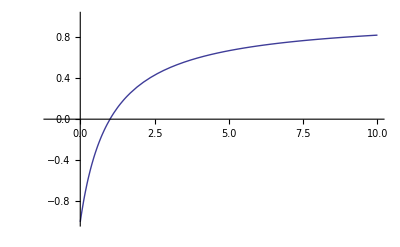

```mathematica
Plot[(c-1)/(c+1),{c,-1,10},PlotRange-> {-1,1}]
```

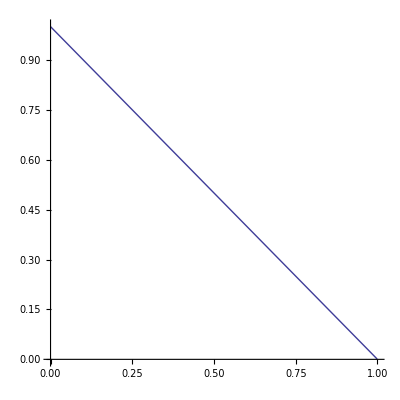

```mathematica
ParametricPlot[{c/(1+c),1/(1+c)},{c,0,1000},PlotRange->{0,1}]
```

```mathematica
Solve[c y/(1-y + c y)==x,y]
```

{{y→x/(c+x-c x)}}

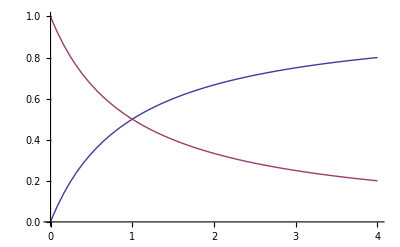

```mathematica
Plot[{c/(1+c),1/(1+c)},{c,0,4}]
```

```mathematica
c/(1+c)-1/(1+c)//FullSimplify
```

(-1+c)/(1+c)

```mathematica
FuncNewVar[x_]:=x/(1-x)
ReplPerpSym
ReplKappa={κ-> (1+x)/(3-x)};
```

{kT→(κ+λ)/2,lT→(κ-λ)/2}

```mathematica
resnotheta//.{kp-> FuncNewVar[x],lp-> FuncNewVar[y]}//FullSimplify
```

-(4^(1+eps) kT lT (-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^(-1/2-eps) (-1+x)^2 (x/(1-x))^(-1-α) (-1+y)^4 (y/(1-y))^(1-α))/((lT^2 (-1+y)^2+y^2) (lT^2 x (-1+y) (-y+x (-1+2 y))+(-1+x) y (-kT^2 y+x (1-y+kT^2 (-1+2 y)))))

### Secdec old

```mathematica
constr={1+(kT-lT)==0,1-(kT-lT)==0,1-(lT+kT)==0};
```

```mathematica
constr2=Join[constr//.{kT->(κ+λ)/2,lT->(κ-λ)/2}//.{κ-> (1+x)/(3-x)}//Factor,{x-3==0}]
```

{1+λ==0,1-λ==0,(2 (-1+x))/(-3+x)==0,-3+x==0}

```mathematica
constr3=constr2/.{x-> x+2}
```

{1+λ==0,1-λ==0,(2 (1+x))/(-1+x)==0,-1+x==0}

```mathematica
res={kT,lT}//.{kT->(κ+λ)/2,lT->(κ-λ)/2}//.{κ-> (3+x)/(1-x)}//Factor
```

{(-3-x-λ+x λ)/(2 (-1+x)),-(3+x-λ+x λ)/(2 (-1+x))}

```mathematica
Solve[#==0]&/@res
```

{{{λ→(3+x)/(-1+x)}},{{λ→(-3-x)/(-1+x)}}}

```mathematica
constr4=constr3/.{λ-> y-1,x-> x-1}/.{x->2 x,y-> 2y}//Factor
```

{2 y==0,-2 (-1+y)==0,(2 x)/(-1+x)==0,2 (-1+x)==0}

```mathematica
Solve[#]&/@constr4
```

{{{y→0}},{{y→1}},{{x→0}},{{x→1}}}

```mathematica
res//Numerator
```

{-3-x-λ+x λ,-3-x+λ-x λ}

```mathematica
res/.{x-> x-1}//Factor
```

{(-2-x-2 λ+x λ)/(2 (-2+x)),-(2+x-2 λ+x λ)/(2 (-2+x))}

```mathematica
res/.{λ-> y-1,x-> x-1}//Factor
```

{(-2 x-2 y+x y)/(2 (-2+x)),-(4-2 y+x y)/(2 (-2+x))}

```mathematica
repl=Thread[{kT,lT}-> res/.{λ-> y-1,x-> x-1}//Factor]
```

{kT→(-2 x-2 y+x y)/(2 (-2+x)),lT→-(4-2 y+x y)/(2 (-2+x))}

```mathematica
(lp (kp (-1+kT^2)+kT^2 lp)+kp (kp+lp) lT^2)//Expand
```

-kp lp+kp kT^2 lp+kT^2 lp^2+kp^2 lT^2+kp lp lT^2

```mathematica
res=(lp (kp (-1+kT^2)+kT^2 lp)+kp (kp+lp) lT^2)//.{kT-> xT+1,lT-> yT+1}//.{xT->(κ+λ)/2,yT->(κ-λ)/2}//.{κ-> x-1,λ-> y-1}/.{x->2 x, y-> 2y}//FullSimplify
```

(kp+(kp+lp) x)^2-2 (kp+lp) (kp+kp x-lp x) y+(kp+lp)^2 y^2

```mathematica
Collect[res,{x,y},]
```

kp^2+(kp^2+2 kp lp+lp^2) x^2+(-2 kp^2-2 kp lp) y+(kp^2+2 kp lp+lp^2) y^2+x (2 kp^2+2 kp lp+(-2 kp^2+2 lp^2) y)

```mathematica
constr//.{kT-> xT+1,lT-> yT+1}//.{xT->(κ+λ)/2,yT->(κ-λ)/2}//.{κ-> x-1,λ-> y-1}/.{x->2 x, y-> 2y}//FullSimplify
```

{y==0,y==1,x==0}

```mathematica
FuncNewVar[x_]:=x/(2-x)
```

```mathematica
x/((2-x)(2-y))
```

```mathematica
constr
```

{1+kT-lT==0,1-kT+lT==0,1-kT-lT==0}

```mathematica
constr//.{kT-> xT/(1-xT),lT-> yT/(1-yT)}//Factor
```

{(1-2 yT+xT yT)/((-1+xT) (-1+yT))==0,(1-2 xT+xT yT)/((-1+xT) (-1+yT))==0,(1-2 xT-2 yT+3 xT yT)/((-1+xT) (-1+yT))==0}

```mathematica
constr//.{kT-> (xT yT)/(1-xT),lT-> (xT yT)/(1-yT)}//Factor
```

{(1-xT-yT+xT yT+xT^2 yT-xT yT^2)/((-1+xT) (-1+yT))==0,-(-1+xT+yT-xT yT+xT^2 yT-xT yT^2)/((-1+xT) (-1+yT))==0,((-1+xT+yT) (-1+xT yT))/((-1+xT) (-1+yT))==0}

```mathematica
newconstr=constr//.{kT-> FuncNewVar[xT],lT-> FuncNewVar[yT]}//Factor
```

{(4-4 yT+xT yT)/((-2+xT) (-2+yT))==0,(4-4 xT+xT yT)/((-2+xT) (-2+yT))==0,(4-4 xT-4 yT+3 xT yT)/((-2+xT) (-2+yT))==0}

```mathematica
constr2=newconstr/.{xT-> xT+1,yT-> yT+1}//Factor//Numerator
```

{(1+xT-3 yT+xT yT)/((-1+xT) (-1+yT))==0,(1-3 xT+yT+xT yT)/((-1+xT) (-1+yT))==0,(-1-xT-yT+3 xT yT)/((-1+xT) (-1+yT))==0}

```mathematica
Solve[constr2[[1]],yT]
```

{{yT→(-1-xT)/(-3+xT)}}

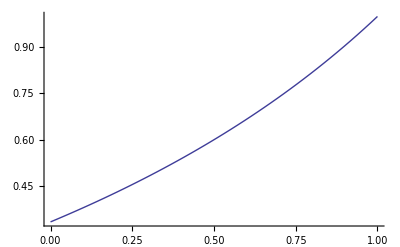

```mathematica
Plot[(-1-xT)/(-3+xT),{xT,0,1}]
```

```mathematica
constr2//.{xT->(κ+λ)/2,yT->(κ-λ)/2}//FullSimplify
```

{1/4 ((-2+κ)^2+8 λ-λ^2),1/4 (4+(-4+κ) κ-λ (8+λ)),1/4 (-4+κ (-4+3 κ)-3 λ^2)}

```mathematica
etasol//.{kT-> 1+lT}//FullSimplify
etasol//.{kT-> -1+lT}//FullSimplify
etasol//.{kT-> 1-lT}//FullSimplify
```

1

1

0

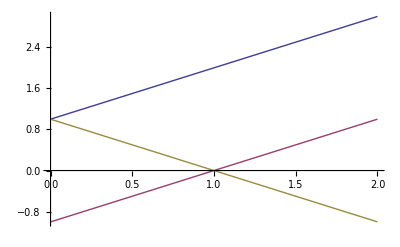

```mathematica
Plot[{1+lT,-1+lT,1-lT},{lT,0,2}]
```

```mathematica
Plot
```

```mathematica
resnotheta
```

-(4^(1+eps) kp^(-1-α) kT lp^(1-α) lT (-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^(-1/2-eps))/((lp^2+lT^2) (lp (kp (-1+kT^2)+kT^2 lp)+kp (kp+lp) lT^2))

```mathematica
resnotheta//.{α-> 0, eps-> 0}//.{kT-> -1+lT+x}//FullSimplify
```

-(4 lp lT (-1+lT+x))/(kp (lp^2+lT^2) √(-(-2+x) x (-2+2 lT+x) (2 lT+x)) ((lp (-1+lT)+kp lT)^2+2 lp (kp+lp) (-1+lT) x+lp (kp+lp) x^2))

```mathematica
Series[resnotheta//.{α-> 0, eps-> 0}//.{kT-> -1+lT+x}//FullSimplify,{x,0,0}]
```

-(4 (lp (-1+lT) lT))/((kp (lp (-1+lT)+kp lT)^2 (lp^2+lT^2) √(-8 lT+8 lT^2)) √x)+√O[x]

```mathematica
Series[resnotheta//.{α-> 0, eps-> 0}//.{kT-> 1+lT+x}//FullSimplify,{x,0,0}]
```

-(√2 lp lT (1+lT))/(kp √(-lT (1+lT)) (lp+(kp+lp) lT)^2 (lp^2+lT^2) √x)+√O[x]

```mathematica
resnotheta//.{α-> 0, eps-> 0}
den=resnotheta//.{α-> 0, eps-> 0}//Denominator
```

-(lp (κ-λ) (κ+λ))/(kp (lp^2+1/4 (κ-λ)^2) √(-(-1+(κ-λ)/2+(κ+λ)/2) (1+(κ-λ)/2+(κ+λ)/2) (-1+1/2 (-κ+λ)+(κ+λ)/2) (1+1/2 (-κ+λ)+(κ+λ)/2)) (1/4 kp (kp+lp) (κ-λ)^2+lp (1/4 lp (κ+λ)^2+kp (-1+1/4 (κ+λ)^2))))

kp √(-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT)) (lp^2+lT^2) (lp (kp (-1+kT^2)+kT^2 lp)+kp (kp+lp) lT^2)

```mathematica
resnotheta/.{lT-> lT-1/2,kT-> kT-1/2}//.{kT-> 0,lT-> 0,kp-> lp+ϵ}//FullSimplify
```

-(0^(-1/2-eps) 4^(2+eps) lp^(1-α) (lp+ϵ)^(-1-α))/((1+4 lp^2) ϵ^2)

```mathematica
Apart[1/((lp^2+lT^2) (lp (kp (-1+kT^2)+kT^2 lp)+kp (kp+lp) lT^2))]
```

-1/(lp (kp-kp kT^2+kp^2 lp-kT^2 lp+kp lp^2) (lp^2+lT^2))+(kp (kp+lp))/(lp (kp-kp kT^2+kp^2 lp-kT^2 lp+kp lp^2) (-kp lp+kp kT^2 lp+kT^2 lp^2+kp^2 lT^2+kp lp lT^2))

```mathematica
tmp=resnotheta//.ReplPerpSym//.{α-> 0, eps-> 0}//FullSimplify
```

-(16 lp (κ-λ) (κ+λ))/(kp (4 lp^2+(κ-λ)^2) √(-(-1+κ^2) (-1+λ^2)) (kp^2 (κ-λ)^2+lp^2 (κ+λ)^2+2 kp lp (-2+κ^2+λ^2)))

```mathematica
Series[tmp,{lp, Infinity,3}]
Series[tmp,{kp, Infinity,3}]
```

-(4 (κ-λ))/((kp (κ+λ) √(-(-1+κ^2) (-1+λ^2))) lp^3)+O[1/lp]^4

-(16 (lp (κ+λ)))/(((κ-λ) √(-(-1+κ^2) (-1+λ^2)) (4 lp^2+κ^2-2 κ λ+λ^2)) kp^3)+O[1/kp]^4

```mathematica
ReplPerpSym
```

{kT→(κ+λ)/2,lT→(κ-λ)/2}

```mathematica
{kT==0,lT==0}//.ReplPerpSym
```

{(κ+λ)/2==0,(κ-λ)/2==0}

```mathematica
Solve[{kT==kt,lT==lt}//.ReplPerpSym,{κ,λ}]//.{kt-> kT, lt-> lT}
```

{{κ→kT+lT,λ→kT-lT}}

```mathematica
denlist=List@@den//.ReplPerpSym//FullSimplify
```

{kp,√(-(-1+κ^2) (-1+λ^2)),lp^2+1/4 (κ-λ)^2,1/4 (kp^2 (κ-λ)^2+lp^2 (κ+λ)^2+2 kp lp (-2+κ^2+λ^2))}

```mathematica
Do[Print[Solve[denlist[[i]]==0]],
{i,1,Length[denlist]}]
```

{{kp→0}}

{{κ→-1},{κ→1},{λ→-1},{λ→1}}

{{lp→-1/2 ⅈ (κ-λ)},{lp→1/2 ⅈ (κ-λ)}}

{{κ→(kp^2 λ-lp^2 λ-2 √(kp^3 lp+2 kp^2 lp^2+kp lp^3-kp^3 lp λ^2-2 kp^2 lp^2 λ^2-kp lp^3 λ^2))/(kp^2+2 kp lp+lp^2)},{κ→(kp^2 λ-lp^2 λ+2 √(kp^3 lp+2 kp^2 lp^2+kp lp^3-kp^3 lp λ^2-2 kp^2 lp^2 λ^2-kp lp^3 λ^2))/(kp^2+2 kp lp+lp^2)},{kp→0,lp→0}}

```mathematica
tmp=4denlist[[4]]//.ReplPerpSym//.{κ-> 1+ϵ}//FullSimplify
```

kp^2 (1+ϵ-λ)^2+lp^2 (1+ϵ+λ)^2+2 kp lp (-1+ϵ (2+ϵ)+λ^2)

```mathematica
Collect[tmp,ϵ,Factor]
```

(kp+lp)^2 ϵ^2-2 (kp+lp) ϵ (-kp-lp+kp λ-lp λ)+(-kp+lp+kp λ+lp λ)^2

```mathematica
Solve[2 kp^2+4 kp lp+2 lp^2-2 kp^2 λ+2 lp^2 λ==0,λ]
```

{{λ→(kp+lp)/(kp-lp)}}

```mathematica
tmp//.{κ-> 1}//FullSimplify
tmp//.{λ-> -1}//FullSimplify
tmp//.{λ-> 0}//FullSimplify
tmp//.{λ-> 1}//FullSimplify
```

(-kp+lp+(kp+lp) λ)^2

(kp-lp+(kp+lp) κ)^2

-4 kp lp+(kp+lp)^2 κ^2

(-kp+lp+(kp+lp) κ)^2

```mathematica
Plot[{(kp^2 λ-lp^2 λ+2 √(kp^3 lp+2 kp^2 lp^2+kp lp^3-kp^3 lp λ^2-2 kp^2 lp^2 λ^2-kp lp^3 λ^2))/(kp^2+2 kp lp+lp^2)//.{kp->100, lp-> 10}},{λ,-1,1},PlotRange->{1,5}]
```

-Graphics-

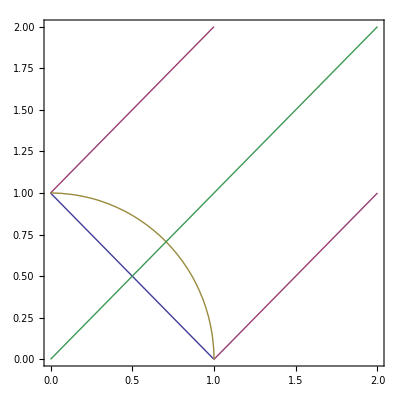

```mathematica
ContourPlot[{deltaqTargFunc[0]==0,deltaqTargFunc[1]==0,lT^2+kT^2-1==0,kT==lT},{kT,0,2},{lT,0,2}]
```

```mathematica
Solve[(kp^2 λ-lp^2 λ+2 √(kp^3 lp+2 kp^2 lp^2+kp lp^3-kp^3 lp λ^2-2 kp^2 lp^2 λ^2-kp lp^3 λ^2))/(kp^2+2 kp lp+lp^2)==1,lp]
```

{{lp→(kp-kp λ)/(1+λ)}}

```mathematica
FuncNewVar[x_]:=x/(1-x)
```

```mathematica
Jaclp=D[FuncNewVar[x],x]//FullSimplify
Jackp=D[FuncNewVar[y],y]//FullSimplify
```

1/(-1+x)^2

1/(-1+y)^2

```mathematica
integrandxy=Jaclp Jackp resnotheta//.{lp-> FuncNewVar[x],kp-> FuncNewVar[y]}//FullSimplify
```

-(4^(1+eps) kT lT (-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^(-1/2-eps) (-1+x) x (x/(1-x))^-α (1/(1-y))^-α (-1+y) y^(-1-α))/((lT^2 (-1+x)^2+x^2) (kT^2 x (-1+y) (-y+x (-1+2 y))+(-1+x) y (-lT^2 y+x (1-y+lT^2 (-1+2 y)))))

```mathematica
den=1/(Times@@Cases[integrandxy//.{eps-> 0, α-> 0},Power[___,n_]/;n<0])
```

√(-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT)) (lT^2 (-1+x)^2+x^2) y (kT^2 x (-1+y) (-y+x (-1+2 y))+(-1+x) y (-lT^2 y+x (1-y+lT^2 (-1+2 y))))

```mathematica
Solve[den==0,{lT}]
```

{{lT→-1-kT},{lT→1-kT},{lT→-1+kT},{lT→1+kT},{lT→-x/(√(-1+2 x-x^2))},{lT→x/(√(-1+2 x-x^2))},{lT→-(ⅈ √x √(-1+y) √(-kT^2 x+y-kT^2 y-x y+2 kT^2 x y))/(√(x y-x^2 y+y^2-3 x y^2+2 x^2 y^2))},{lT→(ⅈ √x √(-1+y) √(-kT^2 x+y-kT^2 y-x y+2 kT^2 x y))/(√(x y-x^2 y+y^2-3 x y^2+2 x^2 y^2))}}

```mathematica
FullSimplify[Solve[den==0,{kT}], kT ϵ Reals]
```

{{kT→-1-lT},{kT→1-lT},{kT→-1+lT},{kT→1+lT},{kT→-(ⅈ √(-1+x) √y √(-lT^2 y+x (1-y+lT^2 (-1+2 y))))/(√(x (-1+y) (-y+x (-1+2 y))))},{kT→(ⅈ √(-1+x) √y √(-lT^2 y+x (1-y+lT^2 (-1+2 y))))/(√(x (-1+y) (-y+x (-1+2 y))))}}

```mathematica
Do[
Print[i, "    ",den//.{x-> i}]
,{i,0,1}]
```

0    lT^4 √(-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT)) y^3

1    kT^2 √(-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT)) (-1+y)^2 y

```mathematica
Do[
Print[i,"     ",den//.{y-> i}]
,{i,0,1}]
```

0     0

1     √(-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT)) (-1+x) (-lT^2+lT^2 x) (lT^2 (-1+x)^2+x^2)

```mathematica
Do[
Print[i," ",j, "    ",den//.{x-> i,y-> j}]
,{i,0,1},{j,0,1}]
```

0 0    0

0 1    lT^4 √(-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))

1 0    0

1 1    0

### Light-cone variables in the range [0,1] and sector decomposition

```mathematica
resnotheta
```

-(4^(1+eps) kp^(-1-α) kT lp^(1-α) lT (-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^(-1/2-eps))/((lp^2+lT^2) (lp (kp (-1+kT^2)+kT^2 lp)+kp (kp+lp) lT^2))

```mathematica
FuncNewVar[x_]:=x/(1-x)
```

```mathematica
Jaclp=D[FuncNewVar[x],x]//FullSimplify
Jackp=D[FuncNewVar[y],y]//FullSimplify
```

1/(-1+x)^2

1/(-1+y)^2

```mathematica
Cases[Series[resnotheta,{lp,0,1},{kp,0,0}]//Normal//PowerExpand,Power[kp|lp,m___]]
Cases[Series[resnotheta,{kp,0,0},{lp,0,0}]//Normal//PowerExpand,Power[kp|lp,m___]]
```

{kp^(-3-α),lp^(1-α)}

{kp^(-1-α),lp^(-1-α)}

```mathematica
integrandxy=Jaclp Jackp resnotheta//.{lp-> FuncNewVar[x],kp-> FuncNewVar[y]}//FullSimplify
```

-(4^(1+eps) kT lT (-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^(-1/2-eps) (-1+x) x (x/(1-x))^-α (1/(1-y))^-α (-1+y) y^(-1-α))/((lT^2 (-1+x)^2+x^2) (kT^2 x (-1+y) (-y+x (-1+2 y))+(-1+x) y (-lT^2 y+x (1-y+lT^2 (-1+2 y)))))

```mathematica
integrandxy//PowerExpand
```

-((-1)^(-1/2-eps) 4^(1+eps) kT (-1+kT-lT)^(-1/2-eps) (1+kT-lT)^(-1/2-eps) lT (-1+kT+lT)^(-1/2-eps) (1+kT+lT)^(-1/2-eps) (1-x)^α (-1+x) x^(1-α) (1-y)^α (-1+y) y^(-1-α))/((lT^2 (-1+x)^2+x^2) (kT^2 x (-1+y) (-y+x (-1+2 y))+(-1+x) y (-lT^2 y+x (1-y+lT^2 (-1+2 y)))))

Sector x > y

```mathematica
integrandxySxgy = x integrandxy/.{y-> x y}
```

-(4^(1+eps) kT lT (-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^(-1/2-eps) (-1+x) x^2 (x/(1-x))^-α (x y)^(-1-α) (1/(1-x y))^-α (-1+x y))/((lT^2 (-1+x)^2+x^2) (kT^2 x (-1+x y) (-x y+x (-1+2 x y))+(-1+x) x y (-lT^2 x y+x (1-x y+lT^2 (-1+2 x y)))))

```mathematica
FullSimplify[integrandxySxgy,x> 0]//PowerExpand
```

-((-1)^(-1/2-eps) 4^(1+eps) kT (-1+kT-lT)^(-1/2-eps) (1+kT-lT)^(-1/2-eps) lT (-1+kT+lT)^(-1/2-eps) (1+kT+lT)^(-1/2-eps) (1-x)^α (-1+x) x^(-1-2 α) y^(-1-α) (1-x y)^α (-1+x y))/((lT^2 (-1+x)^2+x^2) (kT^2 (-1+x y) (-1+(-1+2 x) y)+(-1+x) y (1-x y+lT^2 (-1-y+2 x y))))

```mathematica
Series[integrandxySxgy,{y,0,0},{x,0,0}]//Normal//PowerExpand  (* correct *)
```

-((-1)^(-1/2-eps) 4^(1+eps) (-1+kT-lT)^(-1/2-eps) (1+kT-lT)^(-1/2-eps) (-1+kT+lT)^(-1/2-eps) (1+kT+lT)^(-1/2-eps) x^(-1-2 α) y^(-1-α))/(kT lT)

```mathematica
Series[integrandxySxgy,{x,0,0},{y,0,0}]//Normal//PowerExpand  (* not correct *)
```

-((-1)^(-1/2-eps) 4^(1+eps) (-1+kT-lT)^(-1/2-eps) (1+kT-lT)^(-1/2-eps) (-1+kT+lT)^(-1/2-eps) (1+kT+lT)^(-1/2-eps) x^(-1-2 α) y^(-1-α))/(kT lT)

```mathematica
F[x_,y_]:=(integrandxySxgy/(x^(-1-2 α) y^(-1-α)))
```

```mathematica
tmp=FullSimplify[F[x,y]//PowerExpand,x>0]
```

(ⅈ (-1)^-eps 4^(1+eps) kT (-1+kT-lT)^(-1/2-eps) (1+kT-lT)^(-1/2-eps) lT (-1+kT+lT)^(-1/2-eps) (1+kT+lT)^(-1/2-eps) (1-x)^(1+α) (1-x y)^(1+α))/((lT^2 (-1+x)^2+x^2) (kT^2 (-1+x y) (-1+(-1+2 x) y)+(-1+x) y (1-x y+lT^2 (-1-y+2 x y))))

```mathematica
leadingterm=tmp//.{y-> 0,x-> 0}
```

(ⅈ (-1)^-eps 4^(1+eps) (-1+kT-lT)^(-1/2-eps) (1+kT-lT)^(-1/2-eps) (-1+kT+lT)^(-1/2-eps) (1+kT+lT)^(-1/2-eps))/(kT lT)

```mathematica
tmp=FullSimplify[F[x,y]//PowerExpand,x>0] (Log[x]^(-2α)/x -1)(Log[y]^-α/y-1)
```

(ⅈ (-1)^-eps 4^(1+eps) kT (-1+kT-lT)^(-1/2-eps) (1+kT-lT)^(-1/2-eps) lT (-1+kT+lT)^(-1/2-eps) (1+kT+lT)^(-1/2-eps) (1-x)^(1+α) (1-x y)^(1+α) (-1+Log[x]^(-2 α)/x) (-1+Log[y]^-α/y))/((lT^2 (-1+x)^2+x^2) (kT^2 (-1+x y) (-1+(-1+2 x) y)+(-1+x) y (1-x y+lT^2 (-1-y+2 x y))))

```mathematica
F[x,y]
```

-(4^(1+eps) kT lT (-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^(-1/2-eps) (-1+x) x^(3+2 α) (x/(1-x))^-α y^(1+α) (x y)^(-1-α) (1/(1-x y))^-α (-1+x y))/((lT^2 (-1+x)^2+x^2) (kT^2 x (-1+x y) (-x y+x (-1+2 x y))+(-1+x) x y (-lT^2 x y+x (1-x y+lT^2 (-1+2 x y)))))

```mathematica
tmp2=(tmp/-leadingterm)
```

```mathematica
(*Integrage[leadingterm HeavisideTheta[1+kT-lT,1-kT+lT,-1+kT+lT],{kT,0,Infinity}]*)
```

Integrage[1/(kT lT)ⅈ (-1)^-eps 4^(1+eps) (-1+kT-lT)^(-1/2-eps) (1+kT-lT)^(-1/2-eps) (-1+kT+lT)^(-1/2-eps) (1+kT+lT)^(-1/2-eps) HeavisideTheta[1+kT-lT,1-kT+lT,-1+kT+lT],{kT,0,∞}]

```mathematica
leadingterm//.ReplPerpSym//FullSimplify
```

(ⅈ (-1)^-eps 4^(2+eps) (-1+κ)^(-1/2-eps) (1+κ)^(-1/2-eps) (-1+λ)^(-1/2-eps) (1+λ)^(-1/2-eps))/(κ^2-λ^2)

```mathematica
Integrate[(-1+κ)^(-1/2-eps),κ]
```

(2 (-1+κ)^(1/2-eps))/(1-2 eps)

```mathematica
(*Integrate[leadingterm//.ReplPerpSym//FullSimplify,{λ,-1,1}]*)
```

ConditionalExpression[((-1)^(-2 eps) 4^(2+eps) √π (-1+κ)^(-1/2-eps) (1+κ)^(-1/2-eps) Gamma[1/2-eps] Hypergeometric2F1Regularized[1/2,1,1-eps,1/κ^2])/κ^2,2 Re[eps]<1&&(Re[κ^2]≥1||Re[κ^2]≤0||κ^2∉Reals)]

```mathematica
Series[leadingterm,{kT,kT0,0}]//.{kT0-> 1+lT}
```

(2 ⅈ (-1)^-eps 0^(-1/2-eps) lT^(-3/2-eps) (2+2 lT)^(-1/2-eps))/(1+lT)+O[kT-1-lT]^1

```mathematica
Series[leadingterm,{eps,0,0}]
```

(4 ⅈ)/(kT √(-1+kT-lT) √(1+kT-lT) lT √(-1+kT+lT) √(1+kT+lT))+O[eps]^1

Sector y > x

```mathematica
integrandxySygx = y integrandxy/.{x-> x y}
```

-(4^(1+eps) kT lT (-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^(-1/2-eps) x (1/(1-y))^-α (-1+y) y^(1-α) ((x y)/(1-x y))^-α (-1+x y))/((x^2 y^2+lT^2 (-1+x y)^2) (kT^2 x (-1+y) y (-y+x y (-1+2 y))+y (-1+x y) (-lT^2 y+x y (1-y+lT^2 (-1+2 y)))))

```mathematica
Series[integrandxySygx,{x,0,0},{y,0,0}] (* correct *)
```

(x y)^-α O[x]^1

```mathematica
Series[integrandxySygx,{y,0,0},{x,0,0}] (* not correct *)
```

y^-α (x y)^-α (O[x]^1/y+O[x]^1+O[y]^1)

### Non-linear transformatins

```mathematica
integrandxy
```

-(4^(1+eps) kT lT^3 (-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^(-1/2-eps) (-1+x)^2 (x/(1-x))^-α (y/(1-y))^-α)/((lT^2 (-1+x)^2+x^2) (kT^2 x (-1+y) (-y+x (-1+2 y))+(-1+x) y (-lT^2 y+x (1-y+lT^2 (-1+2 y)))))

```mathematica
integrandxy//.ReplPerpSym//FullSimplify
```

-(4^(1+eps) (-1+x)^2 (x/(1-x))^-α (y/(1-y))^-α (κ-λ)^3 (κ+λ) (-(-1+κ^2) (-1+λ^2))^(-1/2-eps))/((x^2 (4+(κ-λ)^2)+(κ-λ)^2-2 x (κ-λ)^2) (y^2 (κ-λ)^2+2 x y (-2+κ^2+λ^2-2 y (-1+κ^2-κ λ+λ^2))+x^2 ((κ+λ)^2+4 y^2 (-1+κ^2+λ^2)-4 y (-1+κ^2+κ λ+λ^2))))

```mathematica
integrandxy[[9]]
```

(y/(1-y))^-α

## PR28 first

```mathematica
res28=resnotheta kp lp
```

-(4^(1+eps) kp^-α kT lp^(2-α) lT (-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^(-1/2-eps))/((lp^2+lT^2) (lp (kp (-1+kT^2)+kT^2 lp)+kp (kp+lp) lT^2))

```mathematica
integrandxy=Jaclp Jackp res28//.{lp-> FuncNewVar[x],kp-> FuncNewVar[y]}//FullSimplify
```

-(4^(1+eps) kT lT (-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^(-1/2-eps) x^2 (x/(1-x))^-α (y/(1-y))^-α)/((lT^2 (-1+x)^2+x^2) (kT^2 x (-1+y) (-y+x (-1+2 y))+(-1+x) y (-lT^2 y+x (1-y+lT^2 (-1+2 y)))))

```mathematica
integrandxy//PowerExpand
```

-((-1)^(-1/2-eps) 4^(1+eps) kT (-1+kT-lT)^(-1/2-eps) (1+kT-lT)^(-1/2-eps) lT (-1+kT+lT)^(-1/2-eps) (1+kT+lT)^(-1/2-eps) (1-x)^α x^(2-α) (1-y)^α y^-α)/((lT^2 (-1+x)^2+x^2) (kT^2 x (-1+y) (-y+x (-1+2 y))+(-1+x) y (-lT^2 y+x (1-y+lT^2 (-1+2 y)))))

Sector x > y

```mathematica
integrandxySxgy = x integrandxy/.{y-> x y}
```

-(4^(1+eps) kT lT (-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^(-1/2-eps) x^3 (x/(1-x))^-α ((x y)/(1-x y))^-α)/((lT^2 (-1+x)^2+x^2) (kT^2 x (-1+x y) (-x y+x (-1+2 x y))+(-1+x) x y (-lT^2 x y+x (1-x y+lT^2 (-1+2 x y)))))

```mathematica
FullSimplify[integrandxySxgy,x> 0]//PowerExpand
```

-((-1)^(-1/2-eps) 4^(1+eps) kT (-1+kT-lT)^(-1/2-eps) (1+kT-lT)^(-1/2-eps) lT (-1+kT+lT)^(-1/2-eps) (1+kT+lT)^(-1/2-eps) (1-x)^α x^(1-2 α) y^-α (1-x y)^α)/((lT^2 (-1+x)^2+x^2) (kT^2 (-1+x y) (-1+(-1+2 x) y)+(-1+x) y (1-x y+lT^2 (-1-y+2 x y))))

```mathematica
Series[integrandxySxgy,{y,0,0},{x,0,0}]//Normal//PowerExpand  (* correct *)
```

0

```mathematica
Series[integrandxySxgy//.{α-> 0},{eps, 0,0}]
```

-(4 (kT lT x^3))/(√(-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT)) (lT^2 (-1+x)^2+x^2) (kT^2 x (-1+x y) (-x y+x (-1+2 x y))+(-1+x) x y (-lT^2 x y+x (1-x y+lT^2 (-1+2 x y)))))+O[eps]^1

Sector y > x

```mathematica
integrandxySygx = y integrandxy/.{x-> x y}
```

-(4^(1+eps) kT lT (-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^(-1/2-eps) x^2 y^3 (y/(1-y))^-α ((x y)/(1-x y))^-α)/((x^2 y^2+lT^2 (-1+x y)^2) (kT^2 x (-1+y) y (-y+x y (-1+2 y))+y (-1+x y) (-lT^2 y+x y (1-y+lT^2 (-1+2 y)))))

```mathematica
Series[integrandxySygx,{x,0,0},{y,0,0}] (* correct *)
```

(x y)^-α O[x]^2

```mathematica
Series[integrandxySygx//.{α-> 0},{eps, 0,0}]
```

-(4 (kT lT x^2 y^3))/(√(-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT)) (x^2 y^2+lT^2 (-1+x y)^2) (kT^2 x (-1+y) y (-y+x y (-1+2 y))+y (-1+x y) (-lT^2 y+x y (1-y+lT^2 (-1+2 y)))))+O[eps]^1

## PR28 second

```mathematica
res28=resnotheta kp lm//.lsol[[1]]
```

-(4^(1+eps) kp^-α kT lp^-α lT^3 (-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^(-1/2-eps))/((lp^2+lT^2) (lp (kp (-1+kT^2)+kT^2 lp)+kp (kp+lp) lT^2))

```mathematica
integrandxy=Jaclp Jackp res28//.{lp-> FuncNewVar[x],kp-> FuncNewVar[y]}//FullSimplify
```

-(4^(1+eps) kT lT^3 (-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^(-1/2-eps) (-1+x)^2 (x/(1-x))^-α (y/(1-y))^-α)/((lT^2 (-1+x)^2+x^2) (kT^2 x (-1+y) (-y+x (-1+2 y))+(-1+x) y (-lT^2 y+x (1-y+lT^2 (-1+2 y)))))

```mathematica
integrandxy//PowerExpand
```

-((-1)^(-1/2-eps) 4^(1+eps) kT (-1+kT-lT)^(-1/2-eps) (1+kT-lT)^(-1/2-eps) lT^3 (-1+kT+lT)^(-1/2-eps) (1+kT+lT)^(-1/2-eps) (1-x)^α (-1+x)^2 x^-α (1-y)^α y^-α)/((lT^2 (-1+x)^2+x^2) (kT^2 x (-1+y) (-y+x (-1+2 y))+(-1+x) y (-lT^2 y+x (1-y+lT^2 (-1+2 y)))))

Sector x > y

```mathematica
integrandxySxgy = x integrandxy/.{y-> x y}
```

-(4^(1+eps) kT lT^3 (-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^(-1/2-eps) (-1+x)^2 x (x/(1-x))^-α ((x y)/(1-x y))^-α)/((lT^2 (-1+x)^2+x^2) (kT^2 x (-1+x y) (-x y+x (-1+2 x y))+(-1+x) x y (-lT^2 x y+x (1-x y+lT^2 (-1+2 x y)))))

```mathematica
FullSimplify[integrandxySxgy,x> 0]//PowerExpand
```

-((-1)^(-1/2-eps) 4^(1+eps) kT (-1+kT-lT)^(-1/2-eps) (1+kT-lT)^(-1/2-eps) lT^3 (-1+kT+lT)^(-1/2-eps) (1+kT+lT)^(-1/2-eps) (1-x)^α (-1+x)^2 x^(-1-2 α) y^-α (1-x y)^α)/((lT^2 (-1+x)^2+x^2) (kT^2 (-1+x y) (-1+(-1+2 x) y)+(-1+x) y (1-x y+lT^2 (-1-y+2 x y))))

```mathematica
tmp=Series[integrandxySxgy,{y,0,0},{x,0,-1}]//Normal//PowerExpand  (* correct *)
```

-((-1)^(-1/2-eps) 4^(1+eps) (-1+kT-lT)^(-1/2-eps) (1+kT-lT)^(-1/2-eps) lT (-1+kT+lT)^(-1/2-eps) (1+kT+lT)^(-1/2-eps) x^(-1-2 α) y^-α)/kT

```mathematica
tmp2=tmp//.ReplPerpSym//FullSimplify
```

(ⅈ (-1)^-eps 4^(1+eps) x^(-1-2 α) y^-α (-1+κ)^(-1/2-eps) (1+κ)^(-1/2-eps) (κ-λ) (-1+λ)^(-1/2-eps) (1+λ)^(-1/2-eps))/(κ+λ)

```mathematica
Integrate[(-1+κ)^(-1/2-eps) (1+κ)^(-1/2-eps) (κ-λ) /(κ+λ),κ]
```

(-1+κ)^(-1/2-eps) (1+κ)^(-1/2-eps) ((2 λ ((-1+κ)/(κ+λ))^(1/2+eps) ((1+κ)/(κ+λ))^(1/2+eps) AppellF1[1+2 eps,1/2+eps,1/2+eps,2 (1+eps),(1+λ)/(κ+λ),(-1+λ)/(κ+λ)])/(1+2 eps)-(2^(1/2-eps) (1-κ)^(1/2+eps) (1+κ) Hypergeometric2F1[1/2-eps,1/2+eps,3/2-eps,(1+κ)/2])/(-1+2 eps))

```mathematica
Integrate[tmp2,{κ,1,Infinity}]
```

$Aborted

```mathematica
Integrate[tmp2//.eps-> 0,{λ,-1,1}]
```

```mathematica
ConditionalExpression[(4 π x^(-1-2 α) y^-α (-1+2/(√(1-1/κ^2))))/(√(-1+κ) √(1+κ)),Im[κ]≠0||Re[κ]==0||Re[κ]≥1||Re[κ]≤-1]
```

```mathematica
Series[(-1+2/(√(1-1/κ^2)))/(√(-1+κ) √(1+κ))(-1+κ)^(-1/2-eps),{κ,1,0}]
```

(-1+κ)^(-1-eps) (1/(√(κ-1))-1/(√2)+√O[κ-1])

```mathematica
Series[tmp,{eps, 0,0}]
```

-(4 ⅈ lT x^(-1-2 α) y^-α (-1+x α))/(kT √(-1+kT-lT) √(1+kT-lT) √(-1+kT+lT) √(1+kT+lT))+O[eps]^1

```mathematica
Series[integrandxySxgy//.{α-> 0},{eps, 0,0}]
```

-(4 (kT lT x^3))/(√(-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT)) (lT^2 (-1+x)^2+x^2) (kT^2 x (-1+x y) (-x y+x (-1+2 x y))+(-1+x) x y (-lT^2 x y+x (1-x y+lT^2 (-1+2 x y)))))+O[eps]^1

Sector y > x

```mathematica
integrandxySygx = y integrandxy/.{x-> x y}
```

-(4^(1+eps) kT lT (-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^(-1/2-eps) x^2 y^3 (y/(1-y))^-α ((x y)/(1-x y))^-α)/((x^2 y^2+lT^2 (-1+x y)^2) (kT^2 x (-1+y) y (-y+x y (-1+2 y))+y (-1+x y) (-lT^2 y+x y (1-y+lT^2 (-1+2 y)))))

```mathematica
Series[integrandxySygx,{x,0,0},{y,0,0}] (* correct *)
```

(x y)^-α O[x]^2

```mathematica
Series[integrandxySygx//.{α-> 0},{eps, 0,0}]
```

-(4 (kT lT x^2 y^3))/(√(-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT)) (x^2 y^2+lT^2 (-1+x y)^2) (kT^2 x (-1+y) y (-y+x y (-1+2 y))+y (-1+x y) (-lT^2 y+x y (1-y+lT^2 (-1+2 y)))))+O[eps]^1

## Tries

```mathematica
ressub=restmp//.{κ-> 1/γ}//FullSimplify
```

-(4^(2+eps) (-1+1/x)^(1-α) x^2 (-1+1/y)^(-1-α) y^2 (1/γ-λ) (1/γ+λ) (-(-1+1/γ^2) (-1+λ^2))^(-1/2-eps) HeavisideTheta[-1+1/γ,1-λ,1+λ])/(((4 (-1+x)^2)/x^2+(1/γ-λ)^2) (((-1+y)^2 (1/γ-λ)^2)/y^2+((-1+x)^2 (1/γ+λ)^2)/x^2+(2 (-1+x) (-1+y) (-2+1/γ^2+λ^2))/(x y)))

```mathematica
Series[ressub,{λ,1,0}]//Normal//FullSimplify
```

(2^(7/2+2 eps) (-1+1/x)^-α (-1+x) x^5 (-1+1/y)^-α y^5 √(1-1/γ^2) γ^4 ((2-2/γ^2) (-1+λ))^-eps HeavisideTheta[-1+1/γ,1-λ,1+λ])/((-1+y) (x+y-2 x y-x γ+y γ)^2 (x^2-2 x^2 γ+(4+x (-8+5 x)) γ^2) √(-1+λ))

```mathematica
Integrate[(-1+λ)^(-1/2-eps),λ]
```

(2 (-1+λ)^(1/2-eps))/(1-2 eps)

```mathematica
Integrate[(-1+λ)^(-1/2-eps),{λ,L,1}]
```

ConditionalExpression[(2 (-1+L)^(1/2-eps))/(-1+2 eps),Re[eps]<1/2&&Re[L]<1&&Im[L]==0]

```mathematica
restmp//.{κ-> 1/γ}//.{λ-> η/γ}//FullSimplify
```

-((4^(1+eps) (-1+1/x)^-α (-1+x) x^5 (-1+1/y)^-α y^5 γ^2 (-((-4+γ^2) (γ^2-4 η^2))/γ^4)^(-1/2-eps) (-1+η^2) HeavisideTheta[-1+2/γ,1-(2 η)/γ,1+(2 η)/γ])/((-1+y) (γ^2-2 x γ^2+x^2 (γ^2+(-1+η)^2)) (-y^2 (1+η)^2+x^2 (-1+(-1+y) y (-4+γ^2)+2 η-4 y η-(1-2 y)^2 η^2)+x y (-2+γ^2-2 η^2+y (-γ^2+4 (1+η+η^2))))))

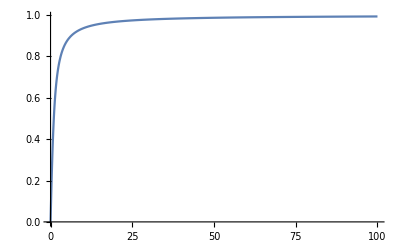

```mathematica
Plot[2/π ArcTan[x],{x,0,100},PlotRange->All]
```

```mathematica
Collect[restmp,{(1-x)^2}]
```

-(4^(1+eps) kp^(-1-α) (-1+1/x)^-α (-1+x) x^5 (κ-λ) (κ+λ) (-(-1+4 κ^2) (-1+4 λ^2))^(-1/2-eps) HeavisideTheta[-1+2 κ,1-2 λ,1+2 λ])/((1-2 x+x^2 (1+κ^2-2 κ λ+λ^2)) (kp^2 x^2 (κ-λ)^2+(-1+x)^2 (κ+λ)^2-kp (-1+x) x (-1+2 κ^2+2 λ^2)))

```mathematica
Series[res,{kT,lT,0}]
```

-(4^(1+eps) kp^(-1-α) lp^(1-α) lT^2 (-1+4 lT^2)^(-1/2-eps))/((lp^2+lT^2) (-kp lp+kp^2 lT^2+2 kp lp lT^2+lp^2 lT^2))+O[kT-lT]^1

```mathematica
Series[FullSimplify[Integrate[(1-x^2)^(-1/2-eps),{x,0,Infinity}],0<Re[eps]<1/2],{eps,0,1}]
```

-ⅈ/(2 eps)+1/2 ⅈ (EulerGamma+PolyGamma[0,1/2])-1/12 ⅈ (3 EulerGamma^2-π^2+6 EulerGamma PolyGamma[0,1/2]+3 PolyGamma[0,1/2]^2) eps+O[eps]^2

```mathematica
respm
```

-(4^(2+eps) kp^(-1-α) lp^(1-α) (κ-λ) (κ+λ) (-(-1+κ^2) (-1+λ^2))^(-1/2-eps) HeavisideTheta[-1+κ,1-λ,1+λ])/((4 lp^2+(κ-λ)^2) (kp^2 (κ-λ)^2+lp^2 (κ+λ)^2+2 kp lp (-2+κ^2+λ^2)))

```mathematica
respm//.{κ-> lp x,λ-> lp y}//FullSimplify
```

-(4^(2+eps) kp^(-1-α) lp^-α (x-y) (x+y) (-(-1+lp^2 x^2) (-1+lp^2 y^2))^(-1/2-eps) HeavisideTheta[-1+lp x,1-lp y,1+lp y])/((4+(x-y)^2) (kp^2 lp (x-y)^2+lp^3 (x+y)^2+2 kp (-2+lp^2 (x^2+y^2))))

### Other

```mathematica
ReplTrans = {qp-> kT+lT, qm-> kT-lT};
ReplInv=(Solve[{qp==xp,qm==xm}//.ReplTrans,{kT,lT}]//Apart)[[1]]
```

{kT→xm/2+xp/2,lT→-xm/2+xp/2}

```mathematica
deltaqTargFunc[eta]//.ReplInv//Simplify
```

-1+xp^2+eta (xm^2-xp^2)

```mathematica
deltaqTargFunc[-1]//.ReplInv//FullSimplify
deltaqTargFunc[0]//.ReplInv//FullSimplify
deltaqTargFunc[1]//.ReplInv//FullSimplify
```

-1-xm^2+2 xp^2

-1+xp^2

-1+xm^2

```mathematica
deltaqTargFuncLCVar[eta_]:=deltaqTargFunc[eta]//.ReplInv
Collect[deltaqTargFuncLCVar[eta]//Simplify,{xp,xm}]
```

-1+eta xm^2+(1-eta) xp^2

```mathematica
(deltaqTargFunc[1/3]==0)//.ReplInv//FullSimplify
```

xm^2+2 xp^2==3

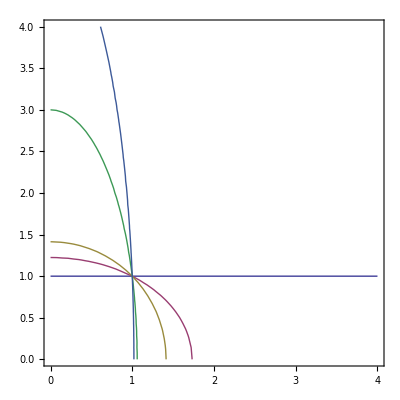

```mathematica
ContourPlot[{deltaqTargFuncLCVar[0]==0,deltaqTargFuncLCVar[1/3]==0,deltaqTargFuncLCVar[1/2]==0,deltaqTargFuncLCVar[8/9]==0,deltaqTargFuncLCVar[0.96]==0},{xm,0,4},{xp,0,4}]
```

```mathematica
ContourPlot[{deltaqTargFunc[0]==0,deltaqTargFunc[1/3]==0,deltaqTargFunc[0.9]==0,deltaqTargFunc[1]==0},{kT,0,2},{lT,0,2}]
```

-Graphics-

```mathematica
kTsol=Solve[(deltaqTarg//.ReplEta)==0,kT]//Simplify
(*JacqT=1/D[(deltaqTarg//.ReplEta),eta]*)
```

{{kT→(-1+2 eta) lT-√(1-4 eta lT^2+4 eta^2 lT^2)},{kT→(-1+2 eta) lT+√(1-4 eta lT^2+4 eta^2 lT^2)}}

(1-kT^2+2 kT lT-lT^2)/(4 kT lT)

1/(4 kT lT)

```mathematica
Series[etasol,{kT,0,0}]
```

(-1+lT^2)/(4 lT kT)+1/2+O[kT]^1

```mathematica
Plot3D[etasol,{kT,0,4},{lT,0,4},PlotRange->{0,1},AxesLabel->{kT,lT}]
```

-Graphics3D-

```mathematica
EtaFunc[Xm_]=etasol//.ReplInv//.{xp-> Xm}//FullSimplify
```

(-1+Xm^2)/(-xm^2+Xm^2)

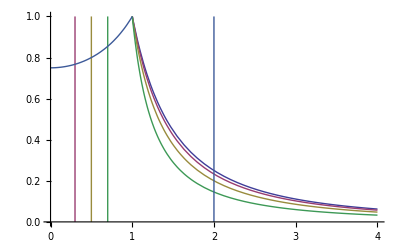

```mathematica
Plot[{EtaFunc[0],EtaFunc[0.3],EtaFunc[0.5],EtaFunc[0.7],EtaFunc[2]},{xm,0,4},PlotRange->{0,1}]
```

```mathematica
sub1=Solve[etasol==0,kT][[2]]
submid=Solve[etasol==1/6,kT][[2]]
sub2=Solve[etasol==1,kT][[2]]
```

{kT→1-lT}

{kT→1/3 (-2 lT+√(9-5 lT^2))}

{kT→1+lT}

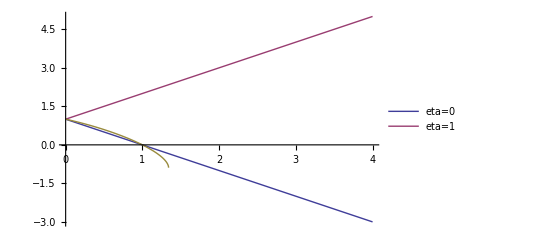

```mathematica
Plot[{kT//.sub1,kT//.sub2,kT//.submid},{lT, 0,4},PlotLegends->{"eta=0","eta=1"}]
```

```mathematica
res=FullSimplify[integralfull JacqT//.{eta-> etasol},kT>0 && lT>0]
```

-(4^(1+eps) kp^(-1-α) kT lp^(1-α) lT (-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^(-1/2-eps))/((lp^2+lT^2) (lp (kp (-1+kT^2)+kT^2 lp)+kp (kp+lp) lT^2))

```mathematica
res//.{lp-> 0}
res//.{kp-> 0}
```

-(0^(1-α) 4^(1+eps) kp^(-3-α) kT (-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^(-1/2-eps))/lT^3

-(0^(-1-α) 4^(1+eps) lp^(-1-α) lT (-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^(-1/2-eps))/(kT (lp^2+lT^2))

```mathematica
Series[res,{kT,0,1}]
Series[res,{lT,0,1}]
```

-(4^(1+eps) kp^(-1-α) lp^(1-α) lT (-1+2 lT^2-lT^4)^(-1/2-eps) kT)/((lp^2+lT^2) (-kp lp+kp^2 lT^2+kp lp lT^2))+O[kT]^2

-(4^(1+eps) kp^(-1-α) kT (-1+2 kT^2-kT^4)^(-1/2-eps) lp^(-1-α) lT)/(-kp lp+kp kT^2 lp+kT^2 lp^2)+O[lT]^2

```mathematica
Series[res,{kT,Infinity,3}]
Series[res,{lT,Infinity,5}]
```

(-kT^4)^-eps ((ⅈ 4^(1+eps) kp^(-1-α) lp^-α lT)/((kp+lp) (lp^2+lT^2) kT^3)+O[1/kT]^4)

(-lT^4)^-eps ((ⅈ 4^(1+eps) kp^(-2-α) kT lp^(1-α))/((kp+lp) lT^5)+O[1/lT]^6)

```mathematica
FullSimplify[integralfull JacqT//.{eta-> etasol},kT>0 && lT>0]//.ReplInv//FullSimplify
```

(4^(2+eps) kp^(-1-α) lp^(1-α) (xm-xp) (xm+xp) (-(-1+xm^2) (-1+xp^2))^(-1/2-eps))/((4 lp^2+(xm-xp)^2) (kp^2 (xm-xp)^2+lp^2 (xm+xp)^2+2 kp lp (-2+xm^2+xp^2)))

```mathematica
Integrate[kT^(-a-4ϵ),kT]
```

kT^(1-a-4 ϵ)/(1-a-4 ϵ)

Integral regular in lT and kT both in the limits 0 and Infinity.

```mathematica
Apart[1/(lp^2+lT^2)]
```

1/(lp^2+lT^2)

```mathematica
Integrate[1/η^(1+ϵ),η]
```

-η^-ϵ/ϵ

```mathematica
Integrate[1/η^(1-ϵ),{η,0,Λ}]
```

ConditionalExpression[Λ^ϵ/ϵ,Re[ϵ]>0]

```mathematica
Integrate[eta^(a1-b1 eps)/eta^n,eta]
```

eta^(1+a1-b1 eps-n)/(1+a1-b1 eps-n)

```mathematica
Integrate[1/kp^(1+α),{kp,0,2En}]
```

ConditionalExpression[-(2^-α En^-α)/α,Re[α]<0]

```mathematica
Integrate[1/(k^(1+α)(1+k^2)),k]
```

(k^-α (2-α+k^2 α Hypergeometric2F1[1,1-α/2,2-α/2,-k^2]))/((-2+α) α)

```mathematica
res=FullSimplify[Integrate[1/(k^(1+α)(1+k^2)),{k,0,Infinity}],α>-2 && α<0]
```

-1/2 π Csc[(π α)/2]

```mathematica
Series[res,{α,0,1}]
```

-1/α-(π^2 α)/24+O[α]^2

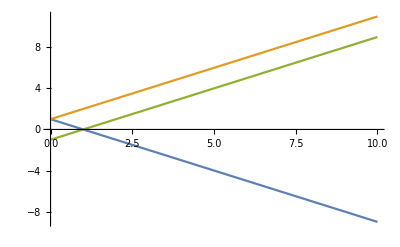

```mathematica
Plot[{1-x,1+x,-1+x},{x,0,10}]
```

```mathematica
Series[Sqrt[kT^2+k3^2]-k3,{k3,0,2}]
```

√(kT^2)-k3+k3^2/(2 √(kT^2))+O[k3]^3

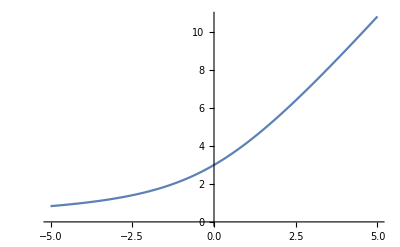

```mathematica
Plot[Sqrt[kT^2+k3^2]+k3//.kT-> 3,{k3,-5,5}]
```

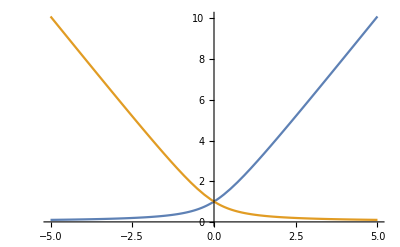

```mathematica
Plot[{Sqrt[1+x^2]+x,Sqrt[1+x^2]-x},{x,-5,5}]
```

```mathematica
integralfull//.{}
```

-(4^(1-eps) (-(-1+eta) eta)^(-1/2-eps) kp^(-1-α) kT^(1-2 eps) lp^(1-α) lT^(1-2 eps))/((lp^2+lT^2) (kT^2 lp^2+2 (1-2 eta) kp kT lp lT+kp^2 lT^2))

```mathematica
res//.{HeavisideTheta[__]-> 1}
```

-(4^(1+eps) kp^(-1-α) kT lp^(1-α) lT (-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^(-1/2-eps))/((lp^2+lT^2) (lp (kp (-1+kT^2)+kT^2 lp)+kp (kp+lp) lT^2))

```mathematica
res2=res//.{HeavisideTheta[__]-> 1}//.{kT-> y kp,lT-> z lp}//.{kp-> λ/y, lp-> κ/z}//FullSimplify
```

-(4^(1+eps) y z κ (κ/z)^(-2-α) λ (λ/y)^(-2-α) (-(-1+κ-λ) (1+κ-λ) (-1+κ+λ) (1+κ+λ))^(-1/2-eps))/((1+z^2) (y^2 κ λ+z^2 κ λ+y z (-1+κ^2+λ^2)))

```mathematica
res2=res//.{HeavisideTheta[__]-> 1}//.{kp-> x/lp,kT-> y kp,lT-> z lp}//FullSimplify
```

-(4^(1+eps) lp^-α x (x/lp)^(-2-α) y z (-((lp^2-x^2 y^2)^2)/lp^4+2 (lp^2+x^2 y^2) z^2-lp^4 z^4)^(-1/2-eps))/((1+z^2) (x^2 y^2+lp^4 z^2+lp^2 (-1+x (y^2+z^2))))

```mathematica
FullSimplify[res2,lp> 0]
```

-(4^(1+eps) lp^2 x^(-1-α) y z (-((lp^2-x^2 y^2)^2)/lp^4+2 (lp^2+x^2 y^2) z^2-lp^4 z^4)^(-1/2-eps))/((1+z^2) (x^2 y^2+lp^4 z^2+lp^2 (-1+x (y^2+z^2))))

```mathematica
vec={kp lp, kT/kp,lT/lp};
```

```mathematica
D[#,{{kp, kT, lT}}]&/@vec//Det
```

1/kp

```mathematica
lp (kp (-1+kT^2)+kT^2 lp)+kp (kp+lp) lT^2//Expand
```

-kp lp+kp kT^2 lp+kT^2 lp^2+kp^2 lT^2+kp lp lT^2

```mathematica
lp (kp (-1+kT^2)+kT^2 lp)+kp (kp+lp) lT^2//.{lT-> y lp,kT-> z kp}//Expand
```

```mathematica
lp (kp (-1+kT^2)+kT^2 lp)+kp (kp+lp) lT^2//.{kp-> x/lp}//Expand
```

kT^2 lp^2-x+kT^2 x+lT^2 x+(lT^2 x^2)/lp^2

```mathematica
lp (kp (-1+kT^2)+kT^2 lp)+kp (kp+lp) lT^2/.{kp-> x/lp,lT-> y lp,kT-> z kp}//Expand
```

-x+lp^2 x y^2+x^2 y^2+kp^2 lp^2 z^2+kp^2 x z^2

```mathematica
respm
```

-(4^(2+eps) kp^(-1-α) lp^(1-α) (κ-λ) (κ+λ) (-(-1+κ^2) (-1+λ^2))^(-1/2-eps) HeavisideTheta[-1+κ,1-λ,1+λ])/((4 lp^2+(κ-λ)^2) (kp^2 (κ-λ)^2+lp^2 (κ+λ)^2+2 kp lp (-2+κ^2+λ^2)))

```mathematica
Integrate[x^(-1-α)/(x^2 a+x b+c),{x,0,Infinity}]
```

$Aborted

```mathematica
(kp^2 (κ-λ)^2+lp^2 (κ+λ)^2+2 kp lp (-2+κ^2+λ^2))//.{kp-> x/(κ-λ),lp-> y/(κ+λ)}
```

x^2+y^2+(2 x y (-2+κ^2+λ^2))/((κ-λ) (κ+λ))

```mathematica
tmpres=Integrate[1/(y+d)(x^(-1-α)y^(1-α))/(x^2+2x y c+y^2),x]
```

1/(2 √((-1+c^2) y^2) (d+y) α)x^-α y^(-1-α) (-2 √((-1+c^2) y^2)+(x/(x+c y-√((-1+c^2) y^2)))^α (c y+√((-1+c^2) y^2)) Hypergeometric2F1[α,α,1+α,(c y-√((-1+c^2) y^2))/(x+c y-√((-1+c^2) y^2))]+(-c y+√((-1+c^2) y^2)) (x/(x+c y+√((-1+c^2) y^2)))^α Hypergeometric2F1[α,α,1+α,(c y+√((-1+c^2) y^2))/(x+c y+√((-1+c^2) y^2))])

```mathematica
Collect[(lp (kp (-1+kT^2)+kT^2 lp)+kp (kp+lp) lT^2),{lp, kp}]
```

kT^2 lp^2+kp^2 lT^2+kp lp (-1+kT^2+lT^2)

```mathematica
tmpres=Integrate[1/(y+d)(x^(-1-α)y^(1-α))/(a x^2+2b x y +c y^2),y]
```

-((x^(-2-α) y^-α (2 (b^2-a c) d x (y/(d+y))^α Hypergeometric2F1[α,α,1+α,d/(d+y)]-(b^2 d x-b d √((b^2-a c) x^2)+a x (-c d+√((b^2-a c) x^2))) ((c y)/(b x-√((b^2-a c) x^2)+c y))^α Hypergeometric2F1[α,α,1+α,(b x-√((b^2-a c) x^2))/(b x-√((b^2-a c) x^2)+c y)]+(-b^2 d x-b d √((b^2-a c) x^2)+a x (c d+√((b^2-a c) x^2))) ((c y)/(b x+√((b^2-a c) x^2)+c y))^α Hypergeometric2F1[α,α,1+α,(b x+√((b^2-a c) x^2))/(b x+√((b^2-a c) x^2)+c y)]))/(2 (-b^2+a c) (c d^2+x (-2 b d+a x)) α))

```mathematica
tmpres//PowerExpand
```

-((x^(-2-α) y^-α (2 (b^2-a c) d x y^α (d+y)^-α Hypergeometric2F1[α,α,1+α,d/(d+y)]-c^α (b^2 d x-b √(b^2-a c) d x+a x (-c d+√(b^2-a c) x)) y^α (b x-√(b^2-a c) x+c y)^-α Hypergeometric2F1[α,α,1+α,(b x-√(b^2-a c) x)/(b x-√(b^2-a c) x+c y)]+c^α (-b^2 d x-b √(b^2-a c) d x+a x (c d+√(b^2-a c) x)) y^α (b x+√(b^2-a c) x+c y)^-α Hypergeometric2F1[α,α,1+α,(b x+√(b^2-a c) x)/(b x+√(b^2-a c) x+c y)]))/(2 (-b^2+a c) (c d^2+x (-2 b d+a x)) α))

```mathematica
tmpres=Integrate[1/(y+d)(x^(-1-α)y^(1-α))/(a x^2+2b x y +c y^2),{y,0,Infinity}]
```

∫_0^∞ (x^(-1-α) y^(1-α))/((d+y) (a x^2+2 b x y+c y^2))ⅆy

```mathematica
res//.{HeavisideTheta[__]-> 1}
```

-(4^(1+eps) .12 kp^(-1-α) kT lp^(1-α) lT (-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^(-1/2-eps))/((lp^2+lT^2) (lp (kp (-1+kT^2)+kT^2 lp)+kp (kp+lp) lT^2))

```mathematica
int0=Integrate[respm,lp]
```

```mathematica
Integrate[y^(-1-α-z)/((a x^2+2b x y +c y^2)^(1+z)),y]
```

(c y^(-z-α) ((b x-√((b^2-a c) x^2)+c y)/(b x-√((b^2-a c) x^2)))^z ((b x+√((b^2-a c) x^2)+c y)/(b x+√((b^2-a c) x^2)))^z (a x^2+y (2 b x+c y))^-z (-a x^2 (2+z^2-3 α+α^2+z (-3+2 α)) AppellF1[-z-α,z,z,1-z-α,-(c y)/(b x+√((b^2-a c) x^2)),(c y)/(-b x+√((b^2-a c) x^2))]+y (z+α) (2 b x (-2+z+α) AppellF1[1-z-α,1+z,1+z,2-z-α,-(c y)/(b x+√((b^2-a c) x^2)),(c y)/(-b x+√((b^2-a c) x^2))]+c y (-1+z+α) AppellF1[2-z-α,1+z,1+z,3-z-α,-(c y)/(b x+√((b^2-a c) x^2)),(c y)/(-b x+√((b^2-a c) x^2))])))/(a x^2 (b x-√((b^2-a c) x^2)) (b x+√((b^2-a c) x^2)) (-2+z+α) (-1+z+α) (z+α))

```mathematica
Integrate[y^(-1-α-z)/((a x^2+2b x y +c y^2)^(1+z)),{y,0,Infinity}]
```

$Aborted

```mathematica
resPF=List@@Apart[1/((y+D)((x+y)^2+A))]
```

{1/((A+D^2-2 D x+x^2) (D+y)),(D-2 x-y)/((A+D^2-2 D x+x^2) (A+x^2+2 x y+y^2))}

```mathematica
integrandlist=List@@Expand[x^(-1-α)  y^(1-β)resPF/.{y-> z-x}//Simplify]
```

{(x^(-1-α) (-x+z)^(1-β))/((A+(D-x)^2) (D-x+z)),(D x^(-1-α) (-x+z)^(1-β))/((A+(D-x)^2) (A+z^2))-(x^-α (-x+z)^(1-β))/((A+(D-x)^2) (A+z^2))-(x^(-1-α) z (-x+z)^(1-β))/((A+(D-x)^2) (A+z^2))}

```mathematica
Integrate[integrandlist[[1]]//.{β-> 0},{x,0,Infinity}]
```

$Aborted

```mathematica
integrandlist[[1]]//.{α-> -1,β-> 1}
```

1/((A+(D-x)^2) (D-x+z))

```mathematica
Integrate[#,x]&/@integrandlist
```

{∫(x^(-1-α) (-x+z)^(1-β))/((A+(D-x)^2) (D-x+z))ⅆx,∫((D x^(-1-α) (-x+z)^(1-β))/((A+(D-x)^2) (A+z^2))-(x^-α (-x+z)^(1-β))/((A+(D-x)^2) (A+z^2))-(x^(-1-α) z (-x+z)^(1-β))/((A+(D-x)^2) (A+z^2)))ⅆx}

```mathematica
resnotheta=res//.{HeavisideTheta[__]-> 1}
```

-(4^(1+eps) .12 kp^(-1-α) kT lp^(1-α) lT (-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^(-1/2-eps))/((lp^2+lT^2) (lp (kp (-1+kT^2)+kT^2 lp)+kp (kp+lp) lT^2))

```mathematica
fac=Times@@Cases[resnotheta,kp^(-α+n_)|lp^(-α+m_)]
```

kp^(-1-α) lp^(1-α)

```mathematica
den=1/Cases[resnotheta,Power[__,-1]]
```

{lp^2+lT^2,lp (kp (-1+kT^2)+kT^2 lp)+kp (kp+lp) lT^2}

```mathematica
feynden=Collect[den[[1]]+den[[2]]x,{lp,kp}]
```

lT^2+kp^2 lT^2 x+lp^2 (1+kT^2 x)+kp lp ((-1+kT^2) x+lT^2 x)

```mathematica
newint=fac/feynden^2
```

(kp^(-1-α) lp^(1-α))/((lT^2+kp^2 lT^2 x+lp^2 (1+kT^2 x)+kp lp ((-1+kT^2) x+lT^2 x))^2)

```mathematica
Integrate[newint,lp]
```

-1/(lT^4 (1+kp^2 x)^2 (-2+α))kp^(-1-α) lp^(2-α) AppellF1[2-α,2,2,3-α,-(2 lp (1+kT^2 x))/(-kp x+kp kT^2 x+kp lT^2 x+√(kp^2 (-1+kT^2+lT^2)^2 x^2-4 lT^2 (1+kp^2 x) (1+kT^2 x))),-(2 lp (1+kT^2 x))/(-kp x+kp kT^2 x+kp lT^2 x-√(kp^2 (-1+kT^2+lT^2)^2 x^2-4 lT^2 (1+kp^2 x) (1+kT^2 x)))]

```mathematica
Integrate[x^a/(x^2+b)^c,{x,0,Infinity}]
```

ConditionalExpression[(b^(1/2 (1+a-2 c)) Gamma[(1+a)/2] Gamma[-1/2-a/2+c])/(2 Gamma[c]),Re[a-2 c]<-1&&(1+a) Arg[1/b]≤2 π&&Re[a]>-1&&Re[b]>0]

```mathematica
int2=fac/Times@@den
```

(kp^(-1-α) lp^(1-α))/((lp^2+lT^2) (lp (kp (-1+kT^2)+kT^2 lp)+kp (kp+lp) lT^2))

```mathematica
int1reg=int2//.{lp^(1-α)-> lp}
```

(kp^(-1-α) lp)/((lp^2+lT^2) (lp (kp (-1+kT^2)+kT^2 lp)+kp (kp+lp) lT^2))

```mathematica
tmp=Integrate[int1reg,{lp,0,Infinity}]
```

∫_0^∞ (kp^(-1-α) lp)/((lp^2+lT^2) (lp (kp (-1+kT^2)+kT^2 lp)+kp (kp+lp) lT^2))ⅆlp

```mathematica
tmp=Integrate[int1reg,lp]
```

(kp^(-1-α) (2 (kp^2+kT^2) lT (-1+kT^2+lT^2) ArcTanh[(2 kT^2 lp+kp (-1+kT^2+lT^2))/(kp √(kT^4+(-1+lT^2)^2-2 kT^2 (1+lT^2)))]+√(kT^4+(-1+lT^2)^2-2 kT^2 (1+lT^2)) (2 kp (-1+kT^2+lT^2) ArcTan[lp/lT]+(kp^2-kT^2) lT (Log[lp^2+lT^2]-Log[kT^2 lp^2+kp^2 lT^2+kp lp (-1+kT^2+lT^2)]))))/(2 lT √(kT^4+(-1+lT^2)^2-2 kT^2 (1+lT^2)) (kp^4 lT^2+kT^4 lT^2+kp^2 (-2 kT^2+kT^4+(-1+lT^2)^2)))

```mathematica
Series[tmp,{lp,Infinity,0}]
```

```mathematica
Limit[tmp,lp-> Infinity]
```

$Aborted

```mathematica
Integrate[int1reg,{lp,0,Infinity}]
```

$Aborted

```mathematica
den[[2]]//Expand
```

-kp lp+kp kT^2 lp+kT^2 lp^2+kp^2 lT^2+kp lp lT^2

```mathematica
Collect[den[[2]],{lp}]
```

kT^2 lp^2+kp^2 lT^2+lp (kp (-1+kT^2)+kp lT^2)

```mathematica
Limit[ArcTanh[x],x-> Infinity]
```

-(ⅈ π)/2

```mathematica
Quit[];
```

```mathematica
<< HypExp`
```

*-*-*-*-*-* HPL 2.0 *-*-*-*-*-*

Author: Daniel Maitre, University of Zurich

Rules for minimal set loaded for weights: 2, 3, 4, 5, 6.

Rules for minimal set for + - weights loaded for weights: 2, 3, 4, 5, 6.

Table of MZVs loaded up to weight 6

Table of values at I loaded up to weight 6

$HPLFunctions gives a list of the functions of the package.
$HPLOptions gives a list of the options of the package.

More info in hep-ph/0507152, hep-ph/0703052 and at 
 http://krone.physik.unizh.ch/~maitreda/HPL/

***********************************
***********  HypExp 2.0  ************
***********************************
Authors:
 Tobias Huber:  RWTH Aachen,

Daniel Maitre: SLAC, University of Zurich.

SetDelayed::write: Tag HypergeometricPFQ in HypergeometricPFQ[mm1 : {___, SeriesData[ϵ_, 0, _, m : 0 | 1, n_, 1], ___}, mm2___List, x_] is Protected.

SetDelayed::write: Tag HypergeometricPFQ in HypergeometricPFQ[mm1___List, mm2 : {___, SeriesData[ϵ_, 0, _, m : 0 | 1, n_, 1], ___}, x_] is Protected.

HypExp loaded! It allows the expansion of hypergeometric functions around their parameters. 
 The new provided commands are:
 - HypExp
 - HypExpInt
 - HypExpU
 - HypExpAddToLib
 - HypExpIsKnownToOrder

More info in hep-ph/0507094 and at 
 http://krone.physik.unizh.ch/~maitreda/HypExp/

```mathematica
HypExp[Hypergeometric2F1[α,α,1+α,-(ⅈ (κ-λ))/(2 (lp-1/2 ⅈ (κ-λ)))],α,2]
```

1+α^2 PolyLog[2,-(ⅈ (κ-λ))/(2 (lp-1/2 ⅈ (κ-λ)))]

```mathematica
?HypExp
```

HypExp[Hypergeometric2F1[...],x,ϵ,n] gives the expansion of the Hypergeometric function around ϵ=0 until order ϵ^n

```mathematica
tmp=respm//.{HeavisideTheta[__]-> 1}
```

-(4^(2+eps) .12 kp^(-1-α) lp^(1-α) (κ-λ) (κ+λ) (-(-1+κ^2) (-1+λ^2))^(-1/2-eps))/((4 lp^2+(κ-λ)^2) (kp^2 (κ-λ)^2+lp^2 (κ+λ)^2+2 kp lp (-2+κ^2+λ^2)))

```mathematica
inttmp=Integrate[tmp,lp]
```

```mathematica
hyplist=Cases[inttmp,Hypergeometric2F1[args___],-1]
```

Hypergeometric2F1::argr: Hypergeometric2F1 called with 1 argument; 4 arguments are expected.

```mathematica
hyplist//.{α-> 0}
```

{1,1,1,1,1,1,1,1}

```mathematica
intsub=inttmp//.{Hypergeometric2F1[__]-> 1};
```

Hypergeometric2F1::argr: Hypergeometric2F1 called with 1 argument; 4 arguments are expected.

```mathematica
Series[intsub,{α,0,0}]
```

-1/kp 2^(3+2 eps) .12 (κ-λ) (κ+λ) (-(-1+κ^2) (-1+λ^2))^(-1/2-eps) ((-2 ⅈ lp+κ-λ-κ Log[lp/(lp-1/2 ⅈ (κ-λ))]+λ Log[lp/(lp-1/2 ⅈ (κ-λ))])/((κ-λ)^2 (-8 ⅈ kp+4 kp^2 κ+4 ⅈ kp κ^2-κ^3-4 kp^2 λ-κ^2 λ+4 ⅈ kp λ^2+κ λ^2+λ^3))+(2 ⅈ lp+κ-λ-κ Log[lp/(lp+1/2 ⅈ (κ-λ))]+λ Log[lp/(lp+1/2 ⅈ (κ-λ))])/((κ-λ)^2 (8 ⅈ kp+4 kp^2 κ-4 ⅈ kp κ^2-κ^3-4 kp^2 λ-κ^2 λ-4 ⅈ kp λ^2+κ λ^2+λ^3))-((κ+λ)^2 (2 kp-kp κ^2+lp κ^2+2 lp κ λ-kp λ^2+lp λ^2-2 √(kp^2 (-1+κ^2) (-1+λ^2))-2 kp Log[lp/(lp-(2 kp-kp κ^2-kp λ^2-2 √(kp^2-kp^2 κ^2-kp^2 λ^2+kp^2 κ^2 λ^2))/(κ^2+2 κ λ+λ^2))]+kp κ^2 Log[lp/(lp-(2 kp-kp κ^2-kp λ^2-2 √(kp^2-kp^2 κ^2-kp^2 λ^2+kp^2 κ^2 λ^2))/(κ^2+2 κ λ+λ^2))]+kp λ^2 Log[lp/(lp-(2 kp-kp κ^2-kp λ^2-2 √(kp^2-kp^2 κ^2-kp^2 λ^2+kp^2 κ^2 λ^2))/(κ^2+2 κ λ+λ^2))]+2 √(kp^2 (-1+κ^2) (-1+λ^2)) Log[lp/(lp-(2 kp-kp κ^2-kp λ^2-2 √(kp^2-kp^2 κ^2-kp^2 λ^2+kp^2 κ^2 λ^2))/(κ^2+2 κ λ+λ^2))]))/(2 (-32 kp^3+48 kp^3 κ^2-16 kp^3 κ^4+48 kp^3 λ^2-64 kp^3 κ^2 λ^2+16 kp^3 κ^4 λ^2-16 kp^3 λ^4+16 kp^3 κ^2 λ^4+32 kp^2 √(kp^2 (-1+κ^2) (-1+λ^2))-32 kp^2 κ^2 √(kp^2 (-1+κ^2) (-1+λ^2))+4 kp^2 κ^4 √(kp^2 (-1+κ^2) (-1+λ^2))+κ^6 √(kp^2 (-1+κ^2) (-1+λ^2))+2 κ^5 λ √(kp^2 (-1+κ^2) (-1+λ^2))-32 kp^2 λ^2 √(kp^2 (-1+κ^2) (-1+λ^2))+24 kp^2 κ^2 λ^2 √(kp^2 (-1+κ^2) (-1+λ^2))-κ^4 λ^2 √(kp^2 (-1+κ^2) (-1+λ^2))-4 κ^3 λ^3 √(kp^2 (-1+κ^2) (-1+λ^2))+4 kp^2 λ^4 √(kp^2 (-1+κ^2) (-1+λ^2))-κ^2 λ^4 √(kp^2 (-1+κ^2) (-1+λ^2))+2 κ λ^5 √(kp^2 (-1+κ^2) (-1+λ^2))+λ^6 √(kp^2 (-1+κ^2) (-1+λ^2))))+((κ+λ)^2 (2 kp-kp κ^2+lp κ^2+2 lp κ λ-kp λ^2+lp λ^2+2 √(kp^2 (-1+κ^2) (-1+λ^2))-2 kp Log[lp/(lp-(2 kp-kp κ^2-kp λ^2+2 √(kp^2-kp^2 κ^2-kp^2 λ^2+kp^2 κ^2 λ^2))/(κ^2+2 κ λ+λ^2))]+kp κ^2 Log[lp/(lp-(2 kp-kp κ^2-kp λ^2+2 √(kp^2-kp^2 κ^2-kp^2 λ^2+kp^2 κ^2 λ^2))/(κ^2+2 κ λ+λ^2))]+kp λ^2 Log[lp/(lp-(2 kp-kp κ^2-kp λ^2+2 √(kp^2-kp^2 κ^2-kp^2 λ^2+kp^2 κ^2 λ^2))/(κ^2+2 κ λ+λ^2))]-2 √(kp^2 (-1+κ^2) (-1+λ^2)) Log[lp/(lp-(2 kp-kp κ^2-kp λ^2+2 √(kp^2-kp^2 κ^2-kp^2 λ^2+kp^2 κ^2 λ^2))/(κ^2+2 κ λ+λ^2))]))/(2 (32 kp^3-48 kp^3 κ^2+16 kp^3 κ^4-48 kp^3 λ^2+64 kp^3 κ^2 λ^2-16 kp^3 κ^4 λ^2+16 kp^3 λ^4-16 kp^3 κ^2 λ^4+32 kp^2 √(kp^2 (-1+κ^2) (-1+λ^2))-32 kp^2 κ^2 √(kp^2 (-1+κ^2) (-1+λ^2))+4 kp^2 κ^4 √(kp^2 (-1+κ^2) (-1+λ^2))+κ^6 √(kp^2 (-1+κ^2) (-1+λ^2))+2 κ^5 λ √(kp^2 (-1+κ^2) (-1+λ^2))-32 kp^2 λ^2 √(kp^2 (-1+κ^2) (-1+λ^2))+24 kp^2 κ^2 λ^2 √(kp^2 (-1+κ^2) (-1+λ^2))-κ^4 λ^2 √(kp^2 (-1+κ^2) (-1+λ^2))-4 κ^3 λ^3 √(kp^2 (-1+κ^2) (-1+λ^2))+4 kp^2 λ^4 √(kp^2 (-1+κ^2) (-1+λ^2))-κ^2 λ^4 √(kp^2 (-1+κ^2) (-1+λ^2))+2 κ λ^5 √(kp^2 (-1+κ^2) (-1+λ^2))+λ^6 √(kp^2 (-1+κ^2) (-1+λ^2)))))+O[α]^1

```mathematica
inttmp=Integrate[tmp,kp]
```

(4^(1+eps) .12 kp^-α lp^(-1-α) (κ-λ)^3 (κ+λ) (-(-1+κ^2) (-1+λ^2))^(-1/2-eps) (4 √(lp^2 (-1+κ^2) (-1+λ^2))-((kp (κ-λ)^2)/(kp (κ-λ)^2-2 √(lp^2 (-1+κ^2) (-1+λ^2))+lp (-2+κ^2+λ^2)))^α (2 √(lp^2 (-1+κ^2) (-1+λ^2))+lp (-2+κ^2+λ^2)) Hypergeometric2F1[α,α,1+α,-(2 √(lp^2 (-1+κ^2) (-1+λ^2))-lp (-2+κ^2+λ^2))/(kp (κ-λ)^2-2 √(lp^2 (-1+κ^2) (-1+λ^2))+lp (-2+κ^2+λ^2))]-(2 √(lp^2 (-1+κ^2) (-1+λ^2))-lp (-2+κ^2+λ^2)) ((kp (κ-λ)^2)/(kp (κ-λ)^2+2 √(lp^2 (-1+κ^2) (-1+λ^2))+lp (-2+κ^2+λ^2)))^α Hypergeometric2F1[α,α,1+α,(2 √(lp^2 (-1+κ^2) (-1+λ^2))+lp (-2+κ^2+λ^2))/(kp (κ-λ)^2+2 √(lp^2 (-1+κ^2) (-1+λ^2))+lp (-2+κ^2+λ^2))]))/(α (4 lp^2+(κ-λ)^2) (κ^2-λ^2)^2 √(lp^2 (-1+κ^2) (-1+λ^2)))

```mathematica
cfs=Cases[inttmp,coeffs__ Hypergeometric2F1[args___]-> coeffs,-1]
```

Hypergeometric2F1::argr: Hypergeometric2F1 called with 1 argument; 4 arguments are expected.

{-1,((kp (κ-λ)^2)/(kp (κ-λ)^2-2 √(lp^2 (-1+κ^2) (-1+λ^2))+lp (-2+κ^2+λ^2)))^α,2 √(lp^2 (-1+κ^2) (-1+λ^2))+lp (-2+κ^2+λ^2),-1,2 √(lp^2 (-1+κ^2) (-1+λ^2))-lp (-2+κ^2+λ^2),((kp (κ-λ)^2)/(kp (κ-λ)^2+2 √(lp^2 (-1+κ^2) (-1+λ^2))+lp (-2+κ^2+λ^2)))^α}

```mathematica
Limit[cfs,kp-> 0]
```

{-1,Limit[((kp (κ-λ)^2)/(kp (κ-λ)^2-2 √(lp^2 (-1+κ^2) (-1+λ^2))+lp (-2+κ^2+λ^2)))^α,kp→0],2 √(lp^2 (-1+κ^2) (-1+λ^2))+lp (-2+κ^2+λ^2),-1,2 √(lp^2 (-1+κ^2) (-1+λ^2))-lp (-2+κ^2+λ^2),Limit[((kp (κ-λ)^2)/(kp (κ-λ)^2+2 √(lp^2 (-1+κ^2) (-1+λ^2))+lp (-2+κ^2+λ^2)))^α,kp→0]}

```mathematica
hyplist=Cases[inttmp,Hypergeometric2F1[args___],-1]
```

Hypergeometric2F1::argr: Hypergeometric2F1 called with 1 argument; 4 arguments are expected.

{Hypergeometric2F1[α,α,1+α,-(2 √(lp^2 (-1+κ^2) (-1+λ^2))-lp (-2+κ^2+λ^2))/(kp (κ-λ)^2-2 √(lp^2 (-1+κ^2) (-1+λ^2))+lp (-2+κ^2+λ^2))],Hypergeometric2F1[α,α,1+α,(2 √(lp^2 (-1+κ^2) (-1+λ^2))+lp (-2+κ^2+λ^2))/(kp (κ-λ)^2+2 √(lp^2 (-1+κ^2) (-1+λ^2))+lp (-2+κ^2+λ^2))]}

```mathematica
Limit[hyplist[[1]],kp-> 0]
```

π α Csc[π α]

```mathematica
Series[%,{α,0,0}]
```

1+O[α]^1

```mathematica
Limit[hyplist[[1]],kp-> Infinity]
```

1

```mathematica
hyplist//.{α-> 0}
```

{1,1}

```mathematica
intsub=inttmp//.{Hypergeometric2F1[__]-> 1};
```

Hypergeometric2F1::argr: Hypergeometric2F1 called with 1 argument; 4 arguments are expected.

```mathematica
Series[intsub,{α,0,0}]
```

(4^(1+eps) .12 (κ-λ)^3 (κ+λ) (-(-1+κ^2) (-1+λ^2))^(-1/2-eps) (-(2 √(lp^2 (-1+κ^2) (-1+λ^2))+lp (-2+κ^2+λ^2)) Log[(kp (κ-λ)^2)/(kp (κ-λ)^2-2 √(lp^2 (-1+κ^2) (-1+λ^2))+lp (-2+κ^2+λ^2))]-(2 √(lp^2 (-1+κ^2) (-1+λ^2))-lp (-2+κ^2+λ^2)) Log[(kp (κ-λ)^2)/(kp (κ-λ)^2+2 √(lp^2 (-1+κ^2) (-1+λ^2))+lp (-2+κ^2+λ^2))]))/(lp (4 lp^2+(κ-λ)^2) (κ^2-λ^2)^2 √(lp^2 (-1+κ^2) (-1+λ^2)))+O[α]^1

```mathematica
Series[tttexp2,{eps,0,0}]
```

(16 ⅈ .12 delta[0]^2)/(β^2 √(-1+κ^2) (κ-λ) (κ+λ) √(-1+λ^2))+O[eps]^1

```mathematica
Series[tttexp,{x,0,0}]
```

x^(-1-α) ((ⅈ (-1)^-eps 4^(2+eps) .12 (-1+κ^2)^(-1/2-eps) (-1+λ^2)^(-1/2-eps) delta[0])/(β (κ-λ) (κ+λ))+O[x]^1)

```mathematica
Integrate[tttexp,lp]
```

-(ⅈ (-1)^-eps 2^(3+2 eps) .12 delta (-1+κ^2)^(-1/2-eps) (-1+λ^2)^(-1/2-eps) (-2 Log[lp]+Log[4 lp^2+(κ-λ)^2]))/(β (κ-λ) (κ+λ))

```mathematica
Integrate[tttexp,{lp,0,Infinity}]
```

Integrate::idiv: Integral of 1/lp\ (4\ lp^2 + (κ - λ)^2) does not converge on {0, ∞}.

∫_0^∞ ((-1)^(1/2-eps) 4^(2+eps) .12 delta (-1+κ^2)^(-1/2-eps) (κ-λ) (-1+λ^2)^(-1/2-eps))/(lp β (4 lp^2+(κ-λ)^2) (κ+λ))ⅆlp

```mathematica
Series[tttexp,{y,1,0}]
```

(1-y)^α O[y-1]^1

```mathematica
resnotheta//Expand
```

-(4^(1+eps) kp^(-1-α) kT lp^(1-α) lT (-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^(-1/2-eps))/((lp^2+lT^2) (lp (kp (-1+kT^2)+kT^2 lp)+kp (kp+lp) lT^2))

```mathematica
(lp (kp (-1+kT^2)+kT^2 lp)+kp (kp+lp) lT^2)//Expand
```

-kp lp+kp kT^2 lp+kT^2 lp^2+kp^2 lT^2+kp lp lT^2

```mathematica
resnotheta//Expand
```

-(4^(1+eps) kp^(-1-α) kT lp^(1-α) lT (-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^(-1/2-eps))/((lp^2+lT^2) (lp (kp (-1+kT^2)+kT^2 lp)+kp (kp+lp) lT^2))

```mathematica
(lp (kp (-1+kT^2)+kT^2 lp)+kp (kp+lp) lT^2)//Expand
```

-kp lp+kp kT^2 lp+kT^2 lp^2+kp^2 lT^2+kp lp lT^2

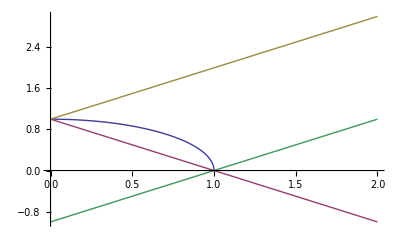

```mathematica
Plot[{Sqrt[1-lT^2],1-lT,1+lT,-1+lT},{lT,0,2}]
```

```mathematica
Clear["δ"]
```

```mathematica
FullSimplify[resnotheta/.{kp-> (1+ kp)/Sqrt[(1+2kp)(1-lp)+kp^2]-1},lp>0 && kp>0]
```

```mathematica
FullSimplify[resnotheta/.{kp-> -(lp kp)/(kp+(1-lp))},lp>0 && kp>0]
```

-(4^(1+eps) kT (1+kp-lp)^2 (-(kp lp^2)/(1+kp-lp))^(-1-α) lT (-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^(-1/2-eps))/((lp^2+lT^2) (kp^2+kT^2 (-1+lp)^2-kp (-1+lp) (1+kT^2-lT^2)))

```mathematica
1/(A x^2+B y^2+ C x y)//Simplify
```

1/(A x^2+C x y+B y^2)

```mathematica
tmpA=resnotheta/.{kp-> kp/lT, lp-> lp/kT}//FullSimplify
```

-(4^(1+eps) kp kT^3 lp (lp/kT)^-α (kp/lT)^(-2-α) lT (-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^(-1/2-eps))/((lp^2+kT^2 lT^2) (kp^2 kT lT+kT lp^2 lT+kp lp (-1+kT^2+lT^2)))

```mathematica
kp^2 kT lT+kT lp^2 lT+kp lp (-1+kT^2+lT^2)//Factor
```

-kp lp+kp kT^2 lp+kp^2 kT lT+kT lp^2 lT+kp lp lT^2

```mathematica
FullSimplify[Solve[{t1==kT^2+lT^2,t2==kT lT},{kT,lT}],t1>0 && t2 >0]
```

{{kT→-(√(t1-√(t1^2-4 t2^2)))/(√2),lT→-(√2 t2)/(√(t1-√(t1^2-4 t2^2)))},{kT→(√(t1-√(t1^2-4 t2^2)))/(√2),lT→(√2 t2)/(√(t1-√(t1^2-4 t2^2)))},{kT→-(√(t1+√(t1^2-4 t2^2)))/(√2),lT→-(√2 t2)/(√(t1+√(t1^2-4 t2^2)))},{kT→(√(t1+√(t1^2-4 t2^2)))/(√2),lT→(√2 t2)/(√(t1+√(t1^2-4 t2^2)))}}

```mathematica
tmpA//.{kT^2-> t1-lT^2, kT -> lT/t2}//FullSimplify
```

(4^(1+eps) lp (kp/lT)^(-1-α) lT^5 ((lp t2)/lT)^-α (-1+lT^2 (2+2/t2^2)-(lT^4 (-1+t2^2)^2)/t2^4)^(-1/2-eps))/((-lp^2+lT^4-lT^2 t1) t2^2 ((kp^2+lp^2) lT^2+kp lp (-1+t1) t2))

```mathematica
resnotheta
```

-(4^(1+eps) kp^(-1-α) kT lp^(1-α) lT (-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^(-1/2-eps))/((lp^2+lT^2) (lp (kp (-1+kT^2)+kT^2 lp)+kp (kp+lp) lT^2))

```mathematica
Integrate[kp^(-3-α-2z2-z3)//.{z2->-1/2,z3->-1/4},kp]
```

kp^(-3/4-α)/(-3/4-α)

```mathematica
Integrate[lp^(-1-α),lp]
```

-lp^-α/α

```mathematica
Collect[(-y+x (-1+2 y))+(-1+x) y (-lT^2 y+x (1-y+lT^2 (-1+2 y))),{x,y},Factor]
```

-y+lT^2 y^2+x (-1+(1+lT^2) y+(1-3 lT^2) y^2)+x^2 (-(-1+lT) (1+lT) y+(-1+2 lT^2) y^2)

```mathematica
Integrate[kp^(-1-α)/(A kp^2+B lp^2+ C kp lp),kp]
```

1/(2 B lp^2 √((-4 A B+C^2) lp^2) α)kp^-α (-2 √((-4 A B+C^2) lp^2)+2^α ((A kp)/(2 A kp+C lp-√((-4 A B+C^2) lp^2)))^α (C lp+√((-4 A B+C^2) lp^2)) Hypergeometric2F1[α,α,1+α,(-C lp+√((-4 A B+C^2) lp^2))/(-2 A kp-C lp+√((-4 A B+C^2) lp^2))]+2^α (-C lp+√((-4 A B+C^2) lp^2)) ((A kp)/(2 A kp+C lp+√((-4 A B+C^2) lp^2)))^α Hypergeometric2F1[α,α,1+α,(C lp+√((-4 A B+C^2) lp^2))/(2 A kp+C lp+√((-4 A B+C^2) lp^2))])

```mathematica
resnotheta
```

-(4^(1+eps) kp^(-1-α) kT lp^(1-α) lT (-(-1+kT-lT) (1+kT-lT) (-1+kT+lT) (1+kT+lT))^(-1/2-eps))/((lp^2+lT^2) (lp (kp (-1+kT^2)+kT^2 lp)+kp (kp+lp) lT^2))

```mathematica
(lp (kp (-1+kT^2)+kT^2 lp)+kp (kp+lp) lT^2)//Expand
```

-kp lp+kp kT^2 lp+kT^2 lp^2+kp^2 lT^2+kp lp lT^2

## Old functions

```mathematica
PrepareForSecDecOld[integral_]:=Module[{res,prodback,tosecdec,toprefac,prefac,ReplSamePower,tosecdecprod,functions,powers,newpowers,positions,newfunctions},
ReplSamePower={Power[f1_,n1_.] Power[f2_,n1_.]-> Power[((f1)(f2)),n1]};

(* split the integral into products *)
res=Cases[integral/.{α-> ap,eps-> ep}//Factor//PowerExpand,Power[P__,n_.]-> {P,n}];
prodback=Product[Power@@res[[i]],{i,1,Length[tmp]}];
If[(prodback/Factor[integral])//PowerExpand//FullSimplify≠1,
Print["Error: PrepareForSecDec does not recover original integral!"]];

(* separate the expression into a prefactor and a function that will be secor-decomposed;prefactor is defined as this part of the expression that will never get zero or singularity in the limit of any variable x->0 *)
(*tosecdec=Cases[res,{f__,pow_}/;(Simplify[(f//.{x-> 0, y-> 0, xT-> 0, yT-> 0})]==0)];
toprefac=Complement[res,tosecdec];
prefac=Product[Power@@toprefac[[i]],{i,1,Length[toprefac]}]//.ReplSamePower//FullSimplify;
*)
Print[res//FullSimplify];
tosecdec=res;
(* expand functions, turn list into product and back into list; this way different powers of the same functions are combined *)
tosecdec=tosecdec//Expand;
tosecdecprod=Product[Power@@tosecdec[[i]],{i,1,Length[tosecdec]}];
tosecdec=Cases[tosecdecprod,Power[P__,n_.]-> {P,n}];

(*tosecdec=Cases[tosecdec,{f_,pow_}/;(pow/.{ep-> 0, ap-> 0})<0];*)

(* combine repeating powers *)
functions=tosecdec[[All,1]];
powers=Pow/@tosecdec[[All,2]];
newpowers=DeleteDuplicates[powers];
positions=Position[powers,#]&/@ newpowers;
newfunctions=Table[Times@@Part[functions,Flatten[positions[[i]]]],{i,1,Length[positions]}];

Return[Int[prefac,newfunctions,newpowers//.Pow-> Sequence]];
]
```

```mathematica
int0=Replace[Id,Power[i_,j_.]-> pow[i,j],1];
int1=int0//.pow[i1_,j_] pow[i2_,j_]-> pow[i1 i2, j];
int2=int1/.{pow[i_,j_]:> pow[Together[i],j]};
int3=int2//.pow[fac_ Power[i_,j_],k_]/;(j<0)-> pow[fac,k] pow[Power[i,-j],-k];
int4=int3//.pow[i1_,j_] pow[i2_,j_]-> pow[i1 i2, j];
int5=int4//.pow[-1+y_,i_] pow[-y_,j_]/;(i==-j)-> pow[1-y,i] pow[y,j]
```

pow[1-x,α] pow[x,-α] pow[1-y,-1+α] pow[y,1-α] pow[(-1+xT)^2 (-x-y+2 x y)^2,1/2+eps] pow[x (-2+xT) xT (-1+y) (-1+yT) (-y+x y-x yT+x y yT),-1/2-eps] pow[8 (-1+x)^3 (-1+y)^5 (x xT+2 y-2 x y-xT y+2 x yT-2 x xT yT-2 x y yT+2 x xT y yT) (-2 x+x xT+2 x y-xT y+2 x yT-2 x xT yT-2 x y yT+2 x xT y yT),1] pow[-(-1+x)^2 (-1+y)^2 (-x-y+2 x y) (x^2 xT^2+8 x xT y-8 x^2 xT y-6 x xT^2 y+4 x^2 xT^2 y-8 x xT y^2+8 x^2 xT y^2+xT^2 y^2+4 x xT^2 y^2-4 x^2 xT^2 y^2+4 x^2 xT yT-4 x^2 xT^2 yT-4 x xT y yT-4 x^2 xT y yT+4 x xT^2 y yT+4 x^2 xT^2 y yT+4 x xT y^2 yT-4 x xT^2 y^2 yT+4 x^2 yT^2-8 x^2 xT yT^2+4 x^2 xT^2 yT^2-8 x^2 y yT^2+16 x^2 xT y yT^2-8 x^2 xT^2 y yT^2+4 x^2 y^2 yT^2-8 x^2 xT y^2 yT^2+4 x^2 xT^2 y^2 yT^2) (x^2 xT^2+4 x xT y-4 x^2 xT y-2 x xT^2 y-2 x^2 xT^2 y+4 y^2-8 x y^2+8 x^2 y^2-4 xT y^2-4 x xT y^2+xT^2 y^2+4 x xT^2 y^2+5 x^2 xT^2 y^2-8 y^3+24 x y^3-24 x^2 y^3+8 xT y^3-20 x xT y^3+28 x^2 xT y^3-2 xT^2 y^3+6 x xT^2 y^3-16 x^2 xT^2 y^3+8 y^4-24 x y^4+20 x^2 y^4-12 xT y^4+36 x xT y^4-32 x^2 xT y^4+5 xT^2 y^4-16 x xT^2 y^4+16 x^2 xT^2 y^4+4 x^2 xT yT-4 x^2 xT^2 yT+8 x y yT-8 x^2 y yT-12 x xT y yT-4 x^2 xT y yT+4 x xT^2 y yT+12 x^2 xT^2 y yT-24 x y^2 yT+24 x^2 y^2 yT+36 x xT y^2 yT-12 x^2 xT y^2 yT-12 x xT^2 y^2 yT-12 x^2 xT^2 y^2 yT+24 x y^3 yT-24 x^2 y^3 yT-36 x xT y^3 yT+20 x^2 xT y^3 yT+12 x xT^2 y^3 yT+4 x^2 xT^2 y^3 yT-8 x y^4 yT+8 x^2 y^4 yT+12 x xT y^4 yT-8 x^2 xT y^4 yT-4 x xT^2 y^4 yT+4 x^2 yT^2-8 x^2 xT yT^2+4 x^2 xT^2 yT^2-16 x^2 y yT^2+32 x^2 xT y yT^2-16 x^2 xT^2 y yT^2+24 x^2 y^2 yT^2-48 x^2 xT y^2 yT^2+24 x^2 xT^2 y^2 yT^2-16 x^2 y^3 yT^2+32 x^2 xT y^3 yT^2-16 x^2 xT^2 y^3 yT^2+4 x^2 y^4 yT^2-8 x^2 xT y^4 yT^2+4 x^2 xT^2 y^4 yT^2),-1]

```mathematica
ReplSamePowers1={pow[i1_,j_] pow[i2_,j_]-> pow[i1 i2, j]};
int1=List@@Id;
int1=Replace[int1,Power[i_,j_.]-> pow[i,j],1];
int1=Times@@int1;
int1=int1//.ReplSamePowers1;
int1=int1/.{pow[i_,j_]:> pow[Together[i],j]};
int1=int1/.{pow[expr__,i_]:>  pow[Numerator[expr],i]pow[Denominator[expr],-i]};
int1=int1//.ReplSamePowers1;
int1=int1//.pow[-1+y_,i_] pow[-y_,j_]/;(i==-j)-> pow[1-y,i] pow[y,j]
```

pow[1-x,α] pow[x,-α] pow[1-y,-1+α] pow[y,1-α] pow[(-1+xT)^2 (-x-y+2 x y)^2,1/2+eps] pow[x (-2+xT) xT (-1+y) (-1+yT) (-y+x y-x yT+x y yT),-1/2-eps] pow[8 (-1+x)^3 (-1+y)^5 (x xT+2 y-2 x y-xT y+2 x yT-2 x xT yT-2 x y yT+2 x xT y yT) (-2 x+x xT+2 x y-xT y+2 x yT-2 x xT yT-2 x y yT+2 x xT y yT),1] pow[-(-1+x)^2 (-1+y)^2 (-x-y+2 x y) (x^2 xT^2+8 x xT y-8 x^2 xT y-6 x xT^2 y+4 x^2 xT^2 y-8 x xT y^2+8 x^2 xT y^2+xT^2 y^2+4 x xT^2 y^2-4 x^2 xT^2 y^2+4 x^2 xT yT-4 x^2 xT^2 yT-4 x xT y yT-4 x^2 xT y yT+4 x xT^2 y yT+4 x^2 xT^2 y yT+4 x xT y^2 yT-4 x xT^2 y^2 yT+4 x^2 yT^2-8 x^2 xT yT^2+4 x^2 xT^2 yT^2-8 x^2 y yT^2+16 x^2 xT y yT^2-8 x^2 xT^2 y yT^2+4 x^2 y^2 yT^2-8 x^2 xT y^2 yT^2+4 x^2 xT^2 y^2 yT^2) (x^2 xT^2+4 x xT y-4 x^2 xT y-2 x xT^2 y-2 x^2 xT^2 y+4 y^2-8 x y^2+8 x^2 y^2-4 xT y^2-4 x xT y^2+xT^2 y^2+4 x xT^2 y^2+5 x^2 xT^2 y^2-8 y^3+24 x y^3-24 x^2 y^3+8 xT y^3-20 x xT y^3+28 x^2 xT y^3-2 xT^2 y^3+6 x xT^2 y^3-16 x^2 xT^2 y^3+8 y^4-24 x y^4+20 x^2 y^4-12 xT y^4+36 x xT y^4-32 x^2 xT y^4+5 xT^2 y^4-16 x xT^2 y^4+16 x^2 xT^2 y^4+4 x^2 xT yT-4 x^2 xT^2 yT+8 x y yT-8 x^2 y yT-12 x xT y yT-4 x^2 xT y yT+4 x xT^2 y yT+12 x^2 xT^2 y yT-24 x y^2 yT+24 x^2 y^2 yT+36 x xT y^2 yT-12 x^2 xT y^2 yT-12 x xT^2 y^2 yT-12 x^2 xT^2 y^2 yT+24 x y^3 yT-24 x^2 y^3 yT-36 x xT y^3 yT+20 x^2 xT y^3 yT+12 x xT^2 y^3 yT+4 x^2 xT^2 y^3 yT-8 x y^4 yT+8 x^2 y^4 yT+12 x xT y^4 yT-8 x^2 xT y^4 yT-4 x xT^2 y^4 yT+4 x^2 yT^2-8 x^2 xT yT^2+4 x^2 xT^2 yT^2-16 x^2 y yT^2+32 x^2 xT y yT^2-16 x^2 xT^2 y yT^2+24 x^2 y^2 yT^2-48 x^2 xT y^2 yT^2+24 x^2 xT^2 y^2 yT^2-16 x^2 y^3 yT^2+32 x^2 xT y^3 yT^2-16 x^2 xT^2 y^3 yT^2+4 x^2 y^4 yT^2-8 x^2 xT y^4 yT^2+4 x^2 xT^2 y^4 yT^2),-1]

```mathematica
PrepareForSecDec[integral_]:=Block[{int,ReplSamePowers,ratio,constfac,pows},
ReplSamePowers={pow[i1_,j_] pow[i2_,j_]-> pow[i1 i2, j]};
int=Replace[integral,Power[i_,j_.]-> pow[i,j],1];
(* combine repating powers *)
int=int//.ReplSamePowers;
int=int/.{pow[i_,j_]:> pow[Together[i],j]};
(* split numerators and denominators under the same pow[] intwo separate pow[] *)
int=int//.pow[fac_ Power[i_,j_],k_]/;(j<0)-> pow[fac,k] pow[Power[i,-j],-k];
int=int//.ReplSamePowers;
(* tranform instances of (-1+x)^a(-x)^a to (1-x)^a x^a *)
int=int//.pow[-1+y_,i_] pow[-y_,j_]/;(i==-j)-> pow[1-y,i] pow[y,j];
(* express negative powers as power -1 *)
int=int//.pow[f_,j_]/;(j<-1)-> pow[Power[f,-j],-1];
int=int//.ReplSamePowers;
(*
(* restore power of -1 *)
ratio=(integral/int)/.pow[i_,j_]:>  Power[i,j]//PowerExpand//FullSimplify;
ratio=ratio/.Power[p_,2 eps] Power[ q_,-2 eps]-> Power[p /q, 2 eps]//FullSimplify;
If[Length[Cases[{ratio},Power[-1,pow__]]]≠ 0,int= ratio int];
*)
(* put constant factors into const[] *)
constfac=int/.pow[__]-> 1/.Power[p_,i_]-> const[p,i];
pows=Times@@Cases[int,pow[__]];
int=constfac pows;
int=int/.{pow[x_Integer,i_]-> const[x,i]};

int=int//.{Power[-1+p_,2]-> Power[1-p,2]};
Return[int];
]
```